## Preamble

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/ecbrown/src/QTAIM.wl/QTAIM

### Parallel Kernels

```mathematica
LaunchKernels[];
```

```mathematica
(*CloseKernels[]*)
```

```mathematica
Needs["QTAIM`"];
ParallelNeeds["QTAIM`"]
```

```mathematica
(* Simple command to test parallel initialization: *)
(*ParallelEvaluate[$QTAIMContoursPositive]*)
```

### MathLink

You may compile a MathLink executable to load Fortran-formatted WFN files.

```mathematica
link=Install[$HomeDirectory<>"/src/QTAIM.wl/QTAIM/QTAIM/qtaim"];
```

```mathematica
(*Uninstall[link];*)
(*ParallelEvaluate[Uninstall[link]];*)
```

## Wavefunction

Import Existing Wavefunction from Web Server:

```mathematica
w=Import["https://ericcbrown.com/QTAIM/wdx/water-cas1010-augccpvtz-opt.wdx"];
```

Alternative ways to import wavefunctions:

### From a WFX on a HTTPS Server (Water)

```mathematica
w=ReadWavefunctionFromWFX["https://ericcbrown.com/QTAIM/wfx/water-hf-ccpvdz-opt.wfx"];
```

### From a WFX on a HTTPS Server (Pyridine)

```mathematica
w=ReadWavefunctionFromWFX["https://ericcbrown.com/QTAIM/wfx/pyridine.wfx"];
```

XML`Parser`XMLGetString::prserr: Expected comment or CDATA at Line: 2 Character: 2.

First::nofirst: {} has zero length and no first element.

ToExpression::notstrbox: First[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

ToExpression::notstrbox: First[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[First[{}]].

ToExpression::notstrbox: First[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[$Failed].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[First[{}],{e→*^,E→*^}].

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[StringReplace[First[{}],{e→*^,E→*^}]].

General::stop: Further output of StringSplit::strse will be suppressed during this calculation.

StringSplit::argb: StringSplit called with 0 arguments; between 1 and 3 arguments are expected.

Table::iterb: Iterator {QTAIM`Private`j,1,$Failed} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Table::nliter: Non-list iterator QTAIM`Private`j at position 2 does not evaluate to a real numeric value.

Table::nliter: Non-list iterator $Failed at position 2 does not evaluate to a real numeric value.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[First[{}],{e→*^,E→*^}].

General::stop: Further output of StringReplace::strse will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression StringSplit[$Failed] cannot be used as a part specification.

### From a WDX on a HTTPS Server (Insulin)

```mathematica
w=Import["https://ericcbrown.com/QTAIM/wdx/insulin_hf.wdx"];
```

### From PySCF

```mathematica
(*session=StartExternalSession["Python"]*)
session=StartExternalSession[<|"System"->"Python","Target"->"/opt/local/bin/python3.8"|>]
```

StartExternalSession::help: For help configuring the Python evaluator, see Configure Python for ExternalEvaluate.

StartExternalSession::replFail: The process for external system Python (/opt/local/bin/python3.8) failed to start.

Failure[…]

```mathematica
importsInput="
from pyscf import gto
from pyscf import lib
from pyscf.x2c import x2c
import numpy
from pyscf import scf, mcscf, symm
from pyscf.tools import molden
";
```

```mathematica
ExternalEvaluate[session,importsInput];
```

ExternalEvaluate::unknownSys: … is not a known system in the ExternalEvaluate Framework.

```mathematica
wavefunctionInput="
mol = gto.M(atom='O 0.0000000000 0.0000000000 0.1182274717; H 0.0000000000 1.4397666095 -0.9948658513; H 0.0000000000 -1.4397666095 -0.9948658513',unit='B', basis='augccpvtz', verbose=1, symmetry=1, symmetry_subgroup='c2v')
mf = scf.RHF(mol).run()
coeff = mf.mo_coeff[:,mf.mo_occ>0]
energy = mf.mo_energy[mf.mo_occ>0]
occ = mf.mo_occ[mf.mo_occ>0]
mc = mcscf.CASSCF(mf, 10, 10)
mc.kernel()
";
```

```mathematica
ExternalEvaluate[session,wavefunctionInput];
```

ExternalEvaluate::unknownSys: … is not a known system in the ExternalEvaluate Framework.

```mathematica
w=ReadWavefunctionFromPySCF[session];
```

ExternalEvaluate::unknownSys: … is not a known system in the ExternalEvaluate Framework.

General::stop: Further output of ExternalEvaluate::unknownSys will be suppressed during this calculation.

Table::iterb: Iterator … does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Table::nliter: Non-list iterator QTAIM`Private`j at position 2 does not evaluate to a real numeric value.

Table::nliter: Non-list iterator … at position 2 does not evaluate to a real numeric value.

```mathematica
DeleteObject[session]
```

DeleteObject::nim: Cannot delete object ….

$Failed

### From a WFN File

```mathematica
ReadWavefunctionFromWFN[filename_]:=Module[
{filenamelength,wfn,lx,ly,lz,l,numberOfNuclei,numberOfOccupiedMolecularOrbitals,numberOfPrimitives,atomicNumbers,nuclearCartesianCoordinates,primitiveTypes,primitiveCenters,primitiveExponents,molecularOrbitalOccupationNumbers,molecularOrbitalPrimitiveCoefficients,energy,virialRatio},

filenamelength=StringLength[filename];

wfn=readwfn[filenamelength,filename];

numberOfNuclei=wfn[[3]];
numberOfOccupiedMolecularOrbitals=wfn[[1]];
atomicNumbers=wfn[[5]];
nuclearCartesianCoordinates=Transpose[Partition[wfn[[4]],numberOfNuclei]];
numberOfPrimitives=wfn[[2]];
primitiveTypes=wfn[[7]];
lx=Table[0,{j,1,numberOfPrimitives}];
ly=Table[0,{j,1,numberOfPrimitives}];
lz=Table[0,{j,1,numberOfPrimitives}];l=Table[Which[primitiveTypes[[j]]==1,{0,0,0},primitiveTypes[[j]]==2,{1,0,0},primitiveTypes[[j]]==3,{0,1,0},primitiveTypes[[j]]==4,{0,0,1},primitiveTypes[[j]]==5,{2,0,0},primitiveTypes[[j]]==6,{0,2,0},primitiveTypes[[j]]==7,{0,0,2},primitiveTypes[[j]]==8,{1,1,0},primitiveTypes[[j]]==9,{1,0,1},primitiveTypes[[j]]==10,{0,1,1},primitiveTypes[[j]]==11,{3,0,0},primitiveTypes[[j]]==12,{0,3,0},primitiveTypes[[j]]==13,{0,0,3},primitiveTypes[[j]]==14,{2,1,0},primitiveTypes[[j]]==15,{2,0,1},primitiveTypes[[j]]==16,{0,2,1},primitiveTypes[[j]]==17,{1,2,0},primitiveTypes[[j]]==18,{1,0,2},primitiveTypes[[j]]==19,{0,1,2},primitiveTypes[[j]]==20,{1,1,1},primitiveTypes[[j]]==21,{4,0,0},primitiveTypes[[j]]==22,{0,4,0},primitiveTypes[[j]]==23,{0,0,4},primitiveTypes[[j]]==24,{3,1,0},primitiveTypes[[j]]==25,{3,0,1},primitiveTypes[[j]]==26,{1,3,0},primitiveTypes[[j]]==27,{0,3,1},primitiveTypes[[j]]==28,{1,0,3},primitiveTypes[[j]]==29,{0,1,3},primitiveTypes[[j]]==30,{2,2,0},primitiveTypes[[j]]==31,{2,0,2},primitiveTypes[[j]]==32,{0,2,2},primitiveTypes[[j]]==33,{2,1,1},primitiveTypes[[j]]==34,{1,2,1},primitiveTypes[[j]]==35,{1,1,2},(*H and higher:# Do IX=0,L # Do IY=0,(L-IX) # IZ=L-IX-IY*)primitiveTypes[[j]]==36,{0,0,5},primitiveTypes[[j]]==37,{0,1,4},primitiveTypes[[j]]==38,{0,2,3},primitiveTypes[[j]]==39,{0,3,2},primitiveTypes[[j]]==40,{0,4,1},primitiveTypes[[j]]==41,{0,5,0},primitiveTypes[[j]]==42,{1,0,4},primitiveTypes[[j]]==43,{1,1,3},primitiveTypes[[j]]==44,{1,2,2},primitiveTypes[[j]]==45,{1,3,1},primitiveTypes[[j]]==46,{1,4,0},primitiveTypes[[j]]==47,{2,0,3},primitiveTypes[[j]]==48,{2,1,2},primitiveTypes[[j]]==49,{2,2,1},primitiveTypes[[j]]==50,{2,3,0},primitiveTypes[[j]]==51,{3,0,2},primitiveTypes[[j]]==52,{3,1,1},primitiveTypes[[j]]==53,{3,2,0},primitiveTypes[[j]]==54,{4,0,1},primitiveTypes[[j]]==55,{4,1,0},primitiveTypes[[j]]==56,{5,0,0}],{j,1,numberOfPrimitives}];lx=l[[All,1]];ly=l[[All,2]];lz=l[[All,3]];

primitiveCenters=wfn[[6]];
primitiveExponents=wfn[[8]];
molecularOrbitalOccupationNumbers=wfn[[9]];
molecularOrbitalPrimitiveCoefficients=wfn[[11]];
energy=wfn[[12,1]];
virialRatio=wfn[[12,2]];

Association[
"NumberOfNuclei"->numberOfNuclei,
"NumberOfOccupiedMolecularOrbitals"->numberOfOccupiedMolecularOrbitals,
"AtomicNumbers"->atomicNumbers,
"NuclearCartesianCoordinates"->nuclearCartesianCoordinates,
"NumberOfPrimitives"->numberOfPrimitives,
"PrimitiveTypes"->primitiveTypes,
"PrimitiveCenters"->primitiveCenters,
"PrimitiveExponents"->primitiveExponents,
"xp"->Table[(nuclearCartesianCoordinates[[primitiveCenters[[j]]]])[[1]],{j,1,numberOfPrimitives}],
"yp"->Table[(nuclearCartesianCoordinates[[primitiveCenters[[j]]]])[[2]],{j,1,numberOfPrimitives}],
"zp"->Table[(nuclearCartesianCoordinates[[primitiveCenters[[j]]]])[[3]],{j,1,numberOfPrimitives}],
"l"->l,
"lx"->lx,
"ly"->ly,
"lz"->lz,
"MolecularOrbitalOccupationNumbers"->molecularOrbitalOccupationNumbers,
"MolecularOrbitalPrimitiveCoefficients"->Partition[molecularOrbitalPrimitiveCoefficients,numberOfPrimitives],
"cFlatten"->Flatten[molecularOrbitalPrimitiveCoefficients],"cTranspose"->Transpose[Transpose[molecularOrbitalPrimitiveCoefficients]],"cFlattenTranspose"->Flatten[Transpose[molecularOrbitalPrimitiveCoefficients]],
"Energy"->energy,
"VirialRatio"->virialRatio]
];
```

```mathematica
(*w=ReadWavefunctionFromWFN["/Users/ecbrown/src/aimpac/c4h4.wfn"];*)
w=ReadWavefunctionFromWFN["/Users/ecbrown/src/QTAIM.wl/resource/water-cas1010-augccpvtz-opt.wfn"];
```

### Export Examples

```mathematica
(*Export["../resource/water-cas1010-augccpvtz-opt.wdx",w]*)
```

```mathematica
(*Export["../resource/water-cas1010-augccpvtz-pyscf.wdx",w]*)
```

```mathematica
(*Export["../resource/water-cas1010-ccpvdz-pyscf.wdx",w]*)
```

```mathematica
(*Export["../resource/insulin_hf.wdx",w]*)
```

## Electron Density and its Derivatives

The electron density, its gradient, and its Hessian convenience functions are defined so that:

```mathematica
rho[w,{0.,0.,0.}]
```

10.7958

```mathematica
g[w,{0.,0.,0.}]
```

{-7.64557×10^-20,-3.95407×10^-17,154.216}

```mathematica
H[w,{0.,0.,0.}]
```

{{-699.31,6.58808×10^-17,1.16299×10^-16},{6.58808×10^-17,-712.381,-1.30566×10^-16},{1.16299×10^-16,-1.30566×10^-16,2374.99}}

## Nuclear Critical Points

```mathematica
ncps=LocateNuclearCriticalPoints[w]//Chop;
```

```mathematica
ncps//TableForm
```

0 | 0 | 0.218693
0 | 1.32401 | -0.809514
0 | -1.32401 | -0.809514

```mathematica
Graphics3D[
Table[
Sphere[ncps[[i]],0.1*((w["AtomicNumbers"])[[i]])]
,{i,1,Length[ncps]}]
]
```

-Graphics3D-

## Bounding Box

```mathematica
bbpad=4;
bbxmin=Floor[Min[ncps[[All,1]]]]-bbpad; 
bbxmax=Ceiling[Max[ncps[[All,1]]]]+bbpad; 
bbymin=Floor[Min[ncps[[All,2]]]]-bbpad; 
bbymax=Ceiling[Max[ncps[[All,2]]]]+bbpad; 
bbzmin=Floor[Min[ncps[[All,3]]]]-bbpad; 
bbzmax=Ceiling[Max[ncps[[All,3]]]]+bbpad; 
bb={{bbxmin,bbxmax},{bbymin,bbymax},{bbzmin,bbzmax}};
```

The bounding box:

```mathematica
N@bb
```

{{-4.,4.},{-6.,6.},{-5.,5.}}

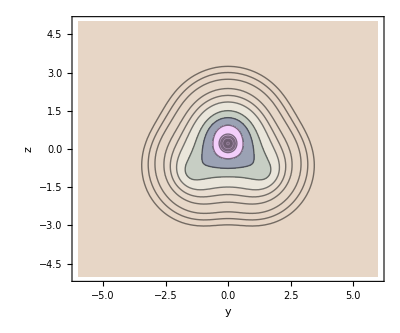

```mathematica
rhoPlot=ContourPlot[
rho[w,{0.,y,z}],
{y,bbymin,bbymax},
{z,bbzmin,bbzmax},
FrameLabel->{"y","z"},
Contours->$QTAIMContoursPositive,
PlotRange->All
,PlotPoints->50
,ColorFunction->"PearlColors"
,ColorFunctionScaling->False
,AspectRatio->Automatic]
```

```mathematica
Graphics3D[
Table[
Sphere[ncps[[i]],0.1*((w["AtomicNumbers"])[[i]])]
,{i,1,Length[ncps]}]
,PlotRange->bb]
```

-Graphics3D-

## Subdivision

### Small Molecules

It is beneficial to make a grid that has the nuclear critical points on the corners.  This only works for small molecules!

```mathematica
xrange=Join[{-Infinity},Sort[DeleteDuplicates[Chop[ncps[[All,1]]],(EuclideanDistance[#1,#2]<10^-6)&]],{Infinity}];
yrange=Join[{-Infinity},Sort[DeleteDuplicates[Chop[ncps[[All,2]]],(EuclideanDistance[#1,#2]<10^-6)&]],{Infinity}];
zrange=Join[{-Infinity},Sort[DeleteDuplicates[Chop[ncps[[All,3]]],(EuclideanDistance[#1,#2]<10^-6)&]],{Infinity}];
```

Make sure the number of subdivisions is reasonable:

```mathematica
Length[
Flatten[
Table[1,
{xmin, 1,Length[xrange]-1},
{ymin, 1,Length[yrange]-1},
{zmin, 1,Length[zrange]-1}
]
,2]
]
```

24

```mathematica
q=AbsoluteTiming[
ParallelSum[
NIntegrate[
If[rho[w,{x,y,z}]>Min[$QTAIMContoursPositive],
rho[w,{x,y,z}],
0
],
{x,xrange[[xmin]],xrange[[xmin+1]]},
{y,yrange[[ymin]],yrange[[ymin+1]]},
{z,zrange[[zmin]],zrange[[zmin+1]]},
Method->{"LocalAdaptive", "SymbolicProcessing"->0}
,AccuracyGoal->4,PrecisionGoal->Infinity],
{xmin, 1,Length[xrange]-1},
{ymin, 1,Length[yrange]-1},
{zmin, 1,Length[zrange]-1}
,Method->"FinestGrained"]
]
```

{3.09926,9.89666}

### Large Molecules

For large molecules, it can be beneficial to make a grid that is on the order of the number of processors one has.

```mathematica
xrange=Subdivide[bbxmin,bbxmax,3];
yrange=Subdivide[bbymin,bbymax,3];
zrange=Subdivide[bbzmin,bbzmax,3];
```

```mathematica
Length[
Flatten[
Table[1,
{xmin, 1,Length[xrange]-1},
{ymin, 1,Length[yrange]-1},
{zmin, 1,Length[zrange]-1}
]
,2]
]
```

27

```mathematica
q=AbsoluteTiming[
NIntegrate[
rho[w,{x,y,z}],
{x,bbxmin,bbxmax},
{y,bbymin,bbymax},
{z,bbzmin,bbzmax},
Method->{"LocalAdaptive", "SymbolicProcessing"->0}
,AccuracyGoal->4,PrecisionGoal->Infinity
]
]
```

{0.566439,9.99946}

### Parallel Example

Here, an even number of subdivisions is helpful so that the nuclear critical points are on a boundary.  Then, NIntegrate will give them special treatment as it does for all boundaries.

```mathematica
xrange=Subdivide[bbxmin,bbxmax,2];
yrange=Subdivide[bbymin,bbymax,2];
zrange=Subdivide[bbzmin,bbzmax,2];

q=AbsoluteTiming[
ParallelSum[
NIntegrate[
rho[w,{x,y,z}],
{x,xrange[[ix]],xrange[[ix+1]]},
{y,xrange[[iy]],xrange[[iy+1]]},
{z,xrange[[iz]],xrange[[iz+1]]},
Method->{"LocalAdaptive", "SymbolicProcessing"->0}
,AccuracyGoal->2,PrecisionGoal->Infinity
]
,{ix,Length[xrange]-1}
,{iy,Length[yrange]-1}
,{iz,Length[zrange]-1}
]
]
```

{0.118139,9.98016}

{0.089777,9.98016}

{0.070798,9.98956}

{0.071745,9.98956}

## Molecular Graph

Evaluate the molecular graph, all critical points corresponding to nuclear, bond, ring, and cage critical points. This may be slower than heuristic methods, e.g. start between two NCPs but it is general, for use in cases where one may not even know where to begin.  (It solves tetrahedrane, see last example.)

(It is normal to see CompiledFunction and other errors here.  These will be quieted in a later version.)

```mathematica
AbsoluteTiming[
cps=LocateCriticalPoints[
{
gx[w,{x,y,z}],
gy[w,{x,y,z}],
gz[w,{x,y,z}]
},
{x,bbxmin,bbxmax},
{y,bbymin,bbymax},
{z,bbzmin,bbzmax}
]
]
```

CompiledFunction::cfne: Numerical error encountered; proceeding with uncompiled evaluation.

Set::shape: Lists {QTAIM`Private`cp000$110424,QTAIM`Private`cp100$110424} and {0,0,0,0,0} are not the same shape.

Part::partd: Part specification QTAIM`Private`cp100$110424⟦1⟧ is longer than depth of object.

Part::partd: Part specification QTAIM`Private`cp000$110424⟦1⟧ is longer than depth of object.

Part::partd: Part specification QTAIM`Private`cp100$110424⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

CompiledFunction::cfne: Numerical error encountered; proceeding with uncompiled evaluation.

Set::shape: Lists {QTAIM`Private`cp000$110453,QTAIM`Private`cp010$110453} and {0,0,0,0,0} are not the same shape.

CompiledFunction::cfne: Numerical error encountered; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfne will be suppressed during this calculation.

Set::shape: Lists {QTAIM`Private`cp000$110462,QTAIM`Private`cp001$110462} and {0,0,0,0,0} are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

FindRoot::nlnum: The function value {4. QTAIM`Private`cp000$110424⟦1⟧ QTAIM`Private`cp100$110424⟦1⟧+4. QTAIM`Private`cp000$110424⟦2⟧ QTAIM`Private`cp100$110424⟦2⟧+«1»+4. «26»⟦4⟧ QTAIM`Private`cp100$110424⟦4⟧+4. QTAIM`Private`cp000$110424⟦5⟧ QTAIM`Private`cp100$110424⟦5⟧,«1»,«1»} is not a list of numbers with dimensions {3} at {x,y,z} = {5.85454×10^-17,1.74847×10^-8,-15.9364}.

FindRoot::nlnum: The function value {4. QTAIM`Private`cp000$110477⟦1⟧ QTAIM`Private`cp100$110477⟦1⟧+4. QTAIM`Private`cp000$110477⟦2⟧ QTAIM`Private`cp100$110477⟦2⟧+«1»+4. «26»⟦4⟧ QTAIM`Private`cp100$110477⟦4⟧+4. QTAIM`Private`cp000$110477⟦5⟧ QTAIM`Private`cp100$110477⟦5⟧,«1»,«1»} is not a list of numbers with dimensions {3} at {x,y,z} = {8.25864×10^-15,6.67763×10^-8,16.507}.

FindRoot::nlnum: The function value {4. QTAIM`Private`cp000$110482⟦1⟧ QTAIM`Private`cp100$110482⟦1⟧+4. QTAIM`Private`cp000$110482⟦2⟧ QTAIM`Private`cp100$110482⟦2⟧+«1»+4. «26»⟦4⟧ QTAIM`Private`cp100$110482⟦4⟧+4. QTAIM`Private`cp000$110482⟦5⟧ QTAIM`Private`cp100$110482⟦5⟧,«1»,«1»} is not a list of numbers with dimensions {3} at {x,y,z} = {5.85454×10^-17,1.74847×10^-8,-15.9364}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

{133.225,{{-1.64478×10^-16,-1.32401,-0.809514},{-1.44992×10^-16,-1.14644,-0.677648},{7.34835×10^-20,1.32401,-0.809514},{7.34835×10^-20,1.32401,-0.809514},{1.60903×10^-19,1.14644,-0.677648},{1.60903×10^-19,1.14644,-0.677648}}}

Characterize the rank and signature, and ellipticity of the critical points with these helper functions:

```mathematica
CriticalPointRank[{x_,y_,z_}]:=Total[Map[If[#==0,0,1]&,Chop[Eigenvalues[H[w,{x,y,z}]]]]];
CriticalPointSignature[{x_,y_,z_}]:=Total[Map[Which[#<0,-1,#==0,0,#>0,1]&,Chop[Eigenvalues[H[w,{x,y,z}]]]]];
Ellipticity[{x_,y_,z_}]:=Module[{evals=Sort[Chop[Eigenvalues[H[w,{x,y,z}],-2]]]},(evals[[1]]/evals[[2]])-1];
```

```mathematica
uniqueCps=DeleteDuplicates[Chop[cps],EuclideanDistance[#1,#2]<1*^-8&]
```

{{0,-1.32401,-0.809514},{0,-1.14644,-0.677648},{0,1.32401,-0.809514},{0,1.14644,-0.677648}}

```mathematica
cpsTable=Select[
Transpose[
{
uniqueCps[[All,1]],
uniqueCps[[All,2]],
uniqueCps[[All,3]],
Map[CriticalPointRank,uniqueCps],
Map[CriticalPointSignature,uniqueCps],
Map[Ellipticity,uniqueCps]
}
]
,#[[5]]!=-3&]
```

{{0,-1.14644,-0.677648,3,-1,-2.39404},{0,1.14644,-0.677648,3,-1,-2.39404}}

```mathematica
Graphics3D[
Join[
Table[
{Black,Sphere[cpsTable[[i,1;;3]],0.1]}
,{i,1,Length[cpsTable]}]
,
Table[
Sphere[ncps[[i]],0.1*((w["AtomicNumbers"])[[i]])]
,{i,1,Length[ncps]}]
]
]
```

-Graphics3D-

```mathematica
bcps=Select[
Transpose[
{
uniqueCps[[All,1]],
uniqueCps[[All,2]],
uniqueCps[[All,3]],
Map[CriticalPointRank,uniqueCps],
Map[CriticalPointSignature,uniqueCps]
}
]
,#[[5]]==-1&];
```

```mathematica
rcps=Select[
Transpose[
{
uniqueCps[[All,1]],
uniqueCps[[All,2]],
uniqueCps[[All,3]],
Map[CriticalPointRank,uniqueCps],
Map[CriticalPointSignature,uniqueCps]
}
]
,#[[5]]==1&];
```

```mathematica
ccps=Select[
Transpose[
{
uniqueCps[[All,1]],
uniqueCps[[All,2]],
uniqueCps[[All,3]],
Map[CriticalPointRank,uniqueCps],
Map[CriticalPointSignature,uniqueCps]
}
]
,#[[5]]==3&];
```

```mathematica
bcps//TableForm
```

0 | -1.14644 | -0.677648 | 3 | -1
0 | 1.14644 | -0.677648 | 3 | -1

```mathematica
rcps//TableForm
```

{}

```mathematica
ccps//TableForm
```

{}

### Parallel Algorithm (WIP)

Unlike the case of integration, it is helpful to make an odd number of divisions, so that the planes of symmetry are not on a boundary.  (Parallelization is probably not necessary or could be worse for small molecules)

```mathematica
(*xrange=Subdivide[bbxmin,bbxmax,3];
yrange=Subdivide[bbymin,bbymax,3];
zrange=Subdivide[bbzmin,bbzmax,3];

AbsoluteTiming[
cps=ParallelTable[
LocateCriticalPoints[
{
gx[w,{x,y,z}],
gy[w,{x,y,z}],
gz[w,{x,y,z}]
},
{x,xrange[[ix]],xrange[[ix+1]]},
{y,yrange[[iy]],yrange[[iy+1]]},
{z,zrange[[iz]],zrange[[iz+1]]}
(*,Method->{"Newton"},Jacobian:>H[w,{x,y,z}]*)
]
,{ix,Length[xrange]-1}
,{iy,Length[yrange]-1}
,{iz,Length[zrange]-1}
]
]*)
```

## Bond Paths

```mathematica
bondPaths=ParallelTable[
BondPath[
w,ncps,bcps[[bp,1;;3]]
]
,{bp,1,Length[bcps]}];
```

```mathematica
bondPathLines3D=ParallelTable[
Line[
Join[
bondPaths[[
bp, (*bp*)
1, (*dir*)
2,1]],
Reverse[bondPaths[[
bp, (*bp*)
2, (*dir*)
2,1]]] 
][[All,2]]
]
,{bp,1,Length[bondPaths]}];
```

```mathematica
graph=Show[
Graphics3D[
bondPathLines3D
]
,
Graphics3D[
Join[
Table[
{Red,Sphere[bcps[[i,1;;3]],0.1]}
,{i,1,Length[bcps]}]
,
Table[
{Green,Sphere[rcps[[i,1;;3]],0.1]}
,{i,1,Length[rcps]}]
,
Table[
{Blue,Sphere[ccps[[i,1;;3]],0.1]}
,{i,1,Length[ccps]}]
,
Table[
Sphere[ncps[[i]],0.1*((w["AtomicNumbers"])[[i]])]
,{i,1,Length[ncps]}]
]
]
]
```

-Graphics3D-

```mathematica
bondPathLines=Table[
Line[
Join[
bondPaths[[
bp, (*bp*)
1, (*dir*)
2,1]],
Reverse[bondPaths[[
bp, (*bp*)
2, (*dir*)
2,1]]] 
][[All,2]][[All,{2,3}]]
]
,{bp,1,Length[bondPaths]}];
```

```mathematica
rhoPlot=ContourPlot[
rho[w,{0.,y,z}],
{y,bbymin,bbymax},
{z,bbzmin,bbzmax},
FrameLabel->{"y","z"},
Contours->$QTAIMContoursPositive,
PlotRange->All
,PlotPoints->50
,ColorFunction->"PearlColors"
,ColorFunctionScaling->False
,AspectRatio->Automatic]
```

-Graphics-

With some trial and error, additional contours illustrate BCPs:

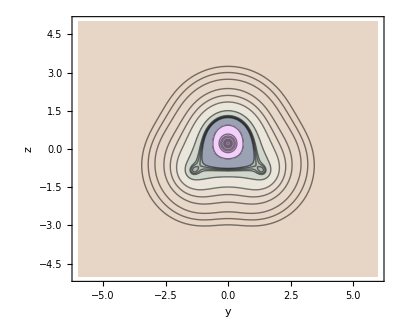

```mathematica
rhoPlot=ContourPlot[
rho[w,{0.,y,z}],
{y,bbymin,bbymax},
{z,bbzmin,bbzmax},
FrameLabel->{"y","z"},
Contours->DeleteDuplicates[Sort[Join[$QTAIMContoursPositive,{13/40,14/40,15/40}]]],
PlotRange->All
,PlotPoints->50
,ColorFunction->"PearlColors"
,ColorFunctionScaling->False
,AspectRatio->Automatic]
```

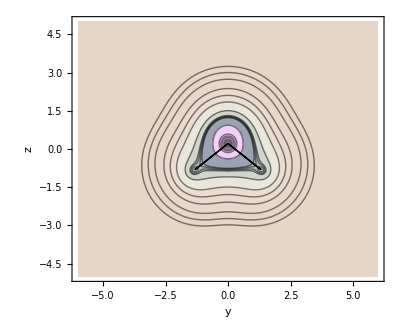

```mathematica
Show[
rhoPlot,
Graphics[bondPathLines]
]
```

## Gradient of the Electron Density

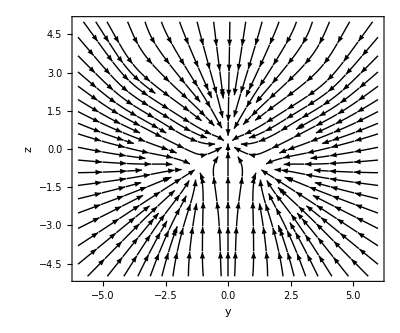

```mathematica
gyz[wfn_,{y_?NumericQ,z_?NumericQ}]:=Rest[g[wfn,{0,y,z}]];

streamPlot=StreamPlot[
gyz[w,{y,z}],
{y,bbymin,bbymax},
{z,bbzmin,bbzmax},
FrameLabel->{"y","z"}
,StreamStyle->Black
,StreamColorFunction->None
,AspectRatio->Automatic]
```

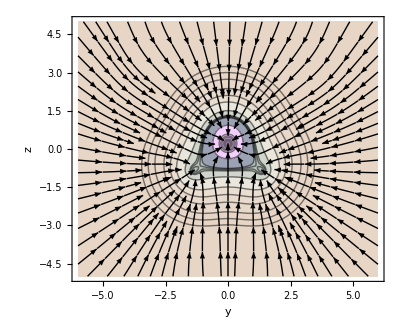

```mathematica
Show[
rhoPlot,
streamPlot
]
```

```mathematica
Show[
SliceContourPlot3D[
rho[w,{x,y,z}],
"CenterPlanes",
{x,bbxmin,bbxmax},
{y,bbymin,bbymax},
{z,bbzmin,bbzmax},
AxesLabel->{"x","y","z"},
Contours->DeleteDuplicates[Sort[Join[$QTAIMContoursPositive,{13/40,14/40,15/40}]]],
PlotRange->{Full,Full,Full,All}
,BoxRatios->Automatic
]
,
graph
]
```

-Graphics3D-

```mathematica
Show[
SliceVectorPlot3D[
g[w,{x,y,z}],
"CenterPlanes",
{x,bbxmin,bbxmax},
{y,bbymin,bbymax},
{z,bbzmin,bbzmax},
AxesLabel->{"x","y","z"},
PlotRange->All
,BoxRatios->Automatic]
,
graph
]
```

-Graphics3D-

## (Negative of the) Laplacian of the Electron Density

It is fairly easy to define custom fields.  For example, the Laplacian, its gradient, and its Hessian can be expressed using the ElectronDensityDerivative convenience function.

```mathematica
laprho[wfn_,{x_?NumericQ,y_?NumericQ,z_?NumericQ}]:=Total[
First[ 
ElectronDensityDerivative[wfn,{{x,y,z}}, 
{{2,0,0},{0,2,0}, {0,0,2}}
]
]
];
gxl[wfn_,{x_?NumericQ,y_?NumericQ,z_?NumericQ}]:=Total[First[ElectronDensityDerivative[wfn,{{x,y,z}}, 
{
{3,0,0},
{1,2,0},
{1,0,2}
}]]];
gyl[wfn_,{x_?NumericQ,y_?NumericQ,z_?NumericQ}]:=Total[First[ElectronDensityDerivative[wfn,{{x,y,z}}, 
{
{2,1,0},
{0,3,0},
{0,1,2}
}]]];
gzl[wfn_,{x_?NumericQ,y_?NumericQ,z_?NumericQ}]:=Total[First[ElectronDensityDerivative[wfn,{{x,y,z}}, 
{
{2,0,1},
{0,2,1},
{0,0,3}
}]]];
gl[wfn_,{x_?NumericQ,y_?NumericQ,z_?NumericQ}]:={
Total[First[ElectronDensityDerivative[wfn,{{x,y,z}}, 
{
{3,0,0},
{1,2,0},
{1,0,2}
}]]],
Total[First[ElectronDensityDerivative[w,{{x,y,z}}, 
{
{2,1,0},
{0,3,0},
{0,1,2}
}]]],
Total[First[ElectronDensityDerivative[w,{{x,y,z}}, 
{
{2,0,1},
{0,2,1},
{0,0,3}
}]]]
};
Hl[wfn_,{x_?NumericQ,y_?NumericQ,z_?NumericQ}]:=Module[
{h},
h={
{
Total[First[ElectronDensityDerivative[wfn,{{x,y,z}}, 
{
{4,0,0},
{2,2,0},
{2,0,2}
}]]],
Total[First[ElectronDensityDerivative[wfn,{{x,y,z}}, 
{
{3,1,0},
{1,3,0},
{1,1,2}
}]]],
Total[First[ElectronDensityDerivative[wfn,{{x,y,z}}, 
{
{3,0,1},
{1,2,1},
{1,0,3}
}]]]
},
{
Total[First[ElectronDensityDerivative[wfn,{{x,y,z}}, 
{
{3,1,0},
{1,3,0},
{1,1,2}
}]]],
Total[First[ElectronDensityDerivative[wfn,{{x,y,z}}, 
{
{2,2,0},
{0,4,0},
{0,2,2}
}]]],
Total[First[ElectronDensityDerivative[wfn,{{x,y,z}}, 
{
{2,1,1},
{0,3,1},
{0,1,3}
}]]]
},
{ 
Total[First[ElectronDensityDerivative[wfn,{{x,y,z}}, 
{
{3,0,1},
{1,2,1},
{1,0,3}
}]]],
Total[First[ElectronDensityDerivative[wfn,{{x,y,z}}, 
{
{2,1,1},
{0,3,1},
{0,1,3}
}]]],
Total[First[ElectronDensityDerivative[wfn,{{x,y,z}}, 
{
{2,0,2},
{0,2,2},
{0,0,4}
}]]]
}
}
];
```

A plot of the Laplacian (unfortunately some “tearing” that needs to be resolved):

```mathematica
SliceContourPlot3D[
-laprho[w,{x,y,z}],
"CenterPlanes",
{x,bbxmin,bbxmax},
{y,bbymin,bbymax},
{z,bbzmin,bbzmax},
AxesLabel->{"x","y","z"},
Contours->$QTAIMContours,
PlotRange->{Full,Full,Full,All}
,BoxRatios->Automatic
,ColorFunction->"PearlColors"
,ColorFunctionScaling->True]
```

-Graphics3D-

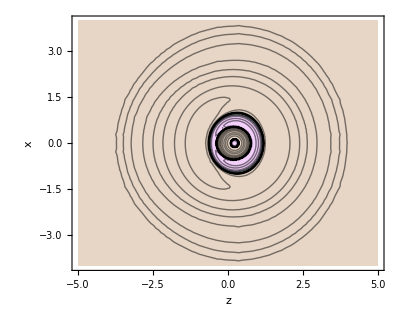

```mathematica
ContourPlot[
-laprho[w,{x,0,z}],
{z,bbzmin,bbzmax},
{x,bbxmin,bbxmax},
FrameLabel->{"z","x"},
Contours->$QTAIMContours,
PlotRange->All
,ColorFunction->"PearlColors"
,ColorFunctionScaling->False
,AspectRatio->Automatic]
```

Locate the critical points in the 3D Negative of Laplacian:

```mathematica
AbsoluteTiming[
cpsl=LocateCriticalPoints[
{
-gxl[w,{x,y,z}],
-gyl[w,{x,y,z}],
-gzl[w,{x,y,z}]
},
{x,bbxmin,bbxmax},
{y,bbymin,bbymax},
{z,bbzmin,bbzmax}
]
]
```

CompiledFunction::cfne: Numerical error encountered; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfne will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

{1318.26,{{-1.26794,1.90386×10^-16,0.941257},{-1.25166,0.661657,-0.0103386},{-1.25166,-0.661657,-0.0103386},{-1.25166,-0.661657,-0.0103386},{-1.25166,-0.661657,-0.0103386},{-0.846583,7.92939×10^-17,-0.850825},{-0.66749,8.92212×10^-17,-0.800568},{-0.578142,-1.27557×10^-18,0.438192},{-0.432089,9.9789×10^-18,-0.786566},{-0.432089,4.96707×10^-17,-0.786566},{-0.277579,1.43229,-1.74983},{-0.277579,-1.43229,-1.74983},{-0.116007,1.20832×10^-17,0.0985677},{-0.000125282,-0.0358367,0.380373},{-3.95952×10^-6,0.0260027,0.382222},{-2.56282×10^-15,-0.534134,-0.206893},{-1.97889×10^-15,2.29192,-0.757691},{-5.13691×10^-16,4.02425×10^-17,-0.852028},{-4.81485×10^-16,1.40626,-1.79305},{-2.7673×10^-16,-3.71271×10^-17,-1.15279},{-1.8862×10^-16,-1.39918,-0.863799},{-1.85156×10^-16,1.193×10^-16,-1.05904},{-9.43756×10^-17,-0.776867,-0.391844},{-1.79333×10^-17,0.662261,0.314336},{-9.3551×10^-18,-1.64277×10^-17,1.59154},{-9.3551×10^-18,-1.34588×10^-16,1.59154},{-9.3551×10^-18,-8.02169×10^-18,1.59154},{-9.3551×10^-18,-8.15996×10^-17,1.59154},{-5.02467×10^-18,1.47004×10^-18,0.846361},{-6.18696×10^-19,0.000145544,0.384262},{-4.07436×10^-19,2.20429,-1.23547},{-1.52212×10^-19,0.955562,0.696681},{-1.52212×10^-19,0.955562,0.696681},{1.65741×10^-20,1.39918,-0.863799},{1.65741×10^-20,1.39918,-0.863799},{9.58653×10^-18,-0.955562,0.696681},{1.23755×10^-17,-0.662261,0.314336},{1.46191×10^-17,-2.55386×10^-17,-0.45298},{1.47718×10^-16,-2.29192,-0.757691},{1.61194×10^-16,-2.29192,-0.757691},{3.99732×10^-16,0.662261,0.314336},{8.43477×10^-16,6.53842×10^-17,-0.45298},{5.51211×10^-6,-0.0275438,0.381973},{0.021711,-0.147984,0.291592},{0.0589623,0.531663,-0.204581},{0.0589623,0.531663,-0.204581},{0.116007,-4.70364×10^-19,0.0985677},{0.277579,1.43229,-1.74983},{0.277579,-1.43229,-1.74983},{0.578142,-4.98123×10^-18,0.438192},{0.578142,8.48563×10^-18,0.438192},{1.25166,-0.661657,-0.0103386},{1.25166,0.661657,-0.0103386},{1.26794,-1.67238×10^-16,0.941257}}}

```mathematica
CriticalPointRank[{x_,y_,z_}]:=Total[Map[If[#==0,0,1]&,Chop[Eigenvalues[-Hl[w,{x,y,z}]]]]];
CriticalPointSignature[{x_,y_,z_}]:=Total[Map[Which[#<0,-1,#==0,0,#>0,1]&,Chop[Eigenvalues[-Hl[w,{x,y,z}]]]]];
```

```mathematica
uniqueCpsl=DeleteDuplicates[Chop[cpsl],EuclideanDistance[#1,#2]<1*^-8&];
```

```mathematica
cpslTable=Select[
Transpose[
{
uniqueCpsl[[All,1]],
uniqueCpsl[[All,2]],
uniqueCpsl[[All,3]],
Map[CriticalPointRank,uniqueCpsl],
Map[CriticalPointSignature,uniqueCpsl]
}
],
#[[5]]==-3&
]
```

{{-0.578142,0,0.438192,3,-3},{0,-0.534134,-0.206893,3,-3},{0,-1.39918,-0.863799,3,-3},{0,1.39918,-0.863799,3,-3},{0.578142,0,0.438192,3,-3}}

Lone Pairs of Electrons on the Oxygen:

```mathematica
Graphics3D[
Join[
Table[
{Blue,Sphere[cpslTable[[i,1;;3]],0.1]}
,{i,1,Length[cpslTable]}]
,
Table[
Sphere[ncps[[i]],0.025*((w["AtomicNumbers"])[[i]])]
,{i,1,Length[ncps]}]
]
]
```

-Graphics3D-

## Better Bond Path Style Using the (Negative of the) Laplacian of the Electron Density

The sign of the Laplacian at the Bond Critical Point can be used to determine whether a bond path should be solid or dashed. The interpolating functions returned by the steepest ascent algorithm are smooth and show banana-like character in good aesthetic detail. Extract the interpolating functions for the forward/backward bond paths:

```mathematica
bondPathInterpolatingFunctions=Table[
{
bondPaths[[
bp, (*bp*)
1, (*dir*)
1]],
Reverse[bondPaths[[
bp, (*bp*)
2, (*dir*)
1]]] 
}
,{bp,1,Length[bondPaths]}];
```

Note the sign of the negative of the Laplacian, we use these to select dashed or solid bond paths:

```mathematica
bcpNegativeLaplacians=Map[(-laprho[w,#]&),bcps[[All,1;;3]]]
```

{2.55995,2.55995}

Generate the bond paths as ParametricPlot3D functions:

```mathematica
bondPathPlots=Table[ 
(* backward *)
s0=(bondPathInterpolatingFunctions[[bcp,All,All]][[1]])[[0]][[1]][[1]][[1]];
sf=(bondPathInterpolatingFunctions[[bcp,All,All]][[1]])[[0]][[1]][[1]][[2]];
forwardPlot=ParametricPlot3D[
(bondPathInterpolatingFunctions[[bcp,All,All]][[1]])/.{QTAIM`Private`s->s}
,{s,s0,sf},PlotStyle->If[bcpNegativeLaplacians[[bcp]]>0,Directive[Black,Thick],Directive[Black,Dashed]],PlotRange->{{-4,4},{-4,4},{-4,4}}];
(* forward *)
s0=(bondPathInterpolatingFunctions[[bcp,All,All]][[2]])[[0]][[1]][[1]][[1]];
sf=(bondPathInterpolatingFunctions[[bcp,All,All]][[2]])[[0]][[1]][[1]][[2]];
backwardPlot=ParametricPlot3D[
(bondPathInterpolatingFunctions[[bcp,All,All]][[2]])/.{QTAIM`Private`s->s}
,{s,s0,sf},PlotStyle->If[bcpNegativeLaplacians[[bcp]]>0,Directive[Black,Thick],Directive[Black,Dashed]],PlotRange->{{-4,4},{-4,4},{-4,4}}];
{forwardPlot,backwardPlot}
,{bcp,1,Length[bcps]}]
```

{{-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-}}

```mathematica
graph=Show[
Graphics3D[
Join[
Table[
{Red,Sphere[bcps[[i,1;;3]],0.1]}
,{i,1,Length[bcps]}]
,
Table[
{Green,Sphere[rcps[[i,1;;3]],0.1]}
,{i,1,Length[rcps]}]
,
Table[
{Blue,Sphere[ccps[[i,1;;3]],0.1]}
,{i,1,Length[ccps]}]
,
Table[
Sphere[ncps[[i]],0.1*((w["AtomicNumbers"])[[i]])]
,{i,1,Length[ncps]}]
]
],
Flatten[bondPathPlots]
]
```

-Graphics3D-

In the plane of the molecule:

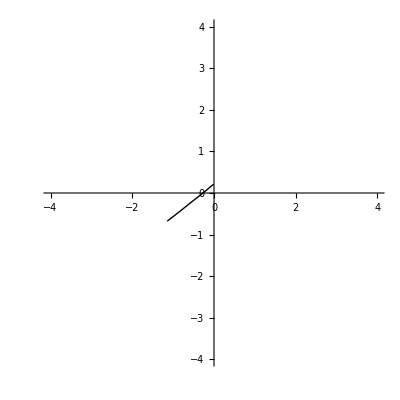
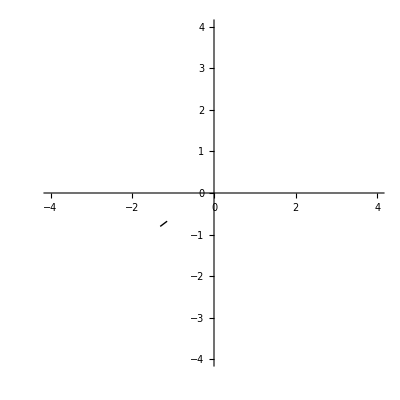
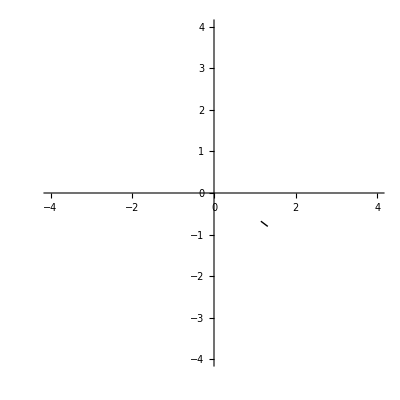
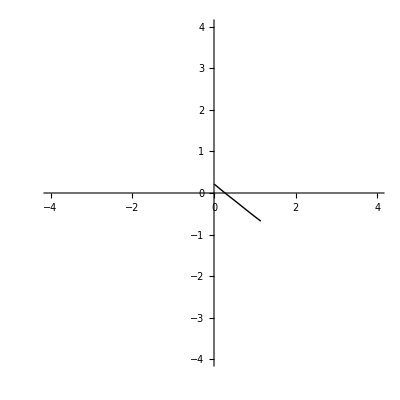

```mathematica
bondPathPlotLines=Table[ 
(* backward *)
s0=(bondPathInterpolatingFunctions[[bcp,All,All]][[1]])[[0]][[1]][[1]][[1]];
sf=(bondPathInterpolatingFunctions[[bcp,All,All]][[1]])[[0]][[1]][[1]][[2]];
forwardPlot=ParametricPlot[
(
(bondPathInterpolatingFunctions[[bcp,All,All]][[1]])/.{QTAIM`Private`s->s}
)[[{2,3}]],{s,s0,sf},PlotStyle->If[bcpNegativeLaplacians[[bcp]]>0,Directive[Black,Thick],Directive[Black,Dashed]],PlotRange->{{-4,4},{-4,4}}];
(* forward *)
s0=(bondPathInterpolatingFunctions[[bcp,All,All]][[2]])[[0]][[1]][[1]][[1]];
sf=(bondPathInterpolatingFunctions[[bcp,All,All]][[2]])[[0]][[1]][[1]][[2]];
backwardPlot=ParametricPlot[
(
(bondPathInterpolatingFunctions[[bcp,All,All]][[2]])/.{QTAIM`Private`s->s}
)[[{2,3}]]
,{s,s0,sf},PlotStyle->If[bcpNegativeLaplacians[[bcp]]>0,Directive[Black,Thick],Directive[Black,Dashed]],PlotRange->{{-4,4},{-4,4}}];
{forwardPlot,backwardPlot}
,{bcp,1,Length[bcps]}]
```

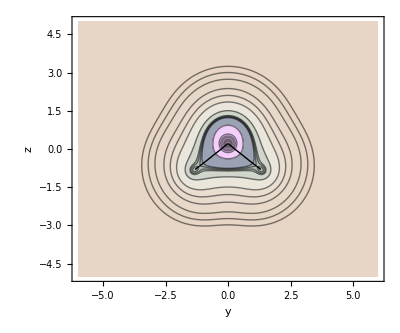

```mathematica
Show[
rhoPlot,
bondPathPlotLines
]
```

## Optimizing the Beta Spheres

```mathematica
q=Reap[
AbsoluteTiming[
NIntegrate[
If[rho[w,{x,y,z}]>Min[$QTAIMContoursPositive],
rho[w,{x,y,z}],
0
], 
{x,bbxmin,bbxmax},
{y,bbymin,bbymax},
{z,bbzmin,bbzmax},
Method->{"LocalAdaptive", "SymbolicProcessing"->0}
,AccuracyGoal->1,PrecisionGoal->Infinity
,EvaluationMonitor:>Sow[{x,y,z}]]
]
];
integrationPoints=q[[2,1]];
```

Determine the associated nuclear attractor for each point.

```mathematica
anas=ParallelMap[
AssociatedNuclearAttractor[w,ncps,#]&,
integrationPoints
];
```

```mathematica
beta0=Table[
otherPoints=Select[
Transpose[
{
integrationPoints,
anas
}
]
,(#[[2]]!=ncp)&][[All,1]];

(80/100)EuclideanDistance[ncps[[ncp]],First@Nearest[otherPoints,ncps[[ncp]],1]]

,{ncp,1,Length[ncps]}]
```

{1.3502,0.482784,0.482784}

### Comparing ODE Integration Methods and the Effects of a better Beta Sphere

#### Default (Conservative) Beta Sphere Radius

```mathematica
AbsoluteTiming[
anasAutomatic=
Map[
AssociatedNuclearAttractor[w,ncps,#,Method->Automatic]&,
integrationPoints
];
]
```

{23.6788,Null}

```mathematica
AbsoluteTiming[
anasAdams=
Map[
AssociatedNuclearAttractor[w,ncps,#,Method->"Adams"]&,
integrationPoints
];
]
```

{23.6459,Null}

```mathematica
AbsoluteTiming[
anasABM=Map[
AssociatedNuclearAttractor[w,ncps,#,Method->"ABM"]&,
integrationPoints
];
]
```

{87.5545,Null}

```mathematica
AbsoluteTiming[
anasBDF=Map[
AssociatedNuclearAttractor[w,ncps,#,Method->"BDF"]&,
integrationPoints
];
]
```

{33.9737,Null}

```mathematica
AbsoluteTiming[
anasBS54=Map[
AssociatedNuclearAttractor[w,ncps,#,Method->"BS54"]&,
integrationPoints
];
]
```

{48.8479,Null}

```mathematica
AbsoluteTiming[
anasCashKarp54=Map[
AssociatedNuclearAttractor[w,ncps,#,Method->"CashKarp45"]&,
integrationPoints
];
]
```

{36.8186,Null}

```mathematica
AbsoluteTiming[
anasDOPRI54=Map[
AssociatedNuclearAttractor[w,ncps,#,Method->"DOPRI54"]&,
integrationPoints
];
]
```

{34.2693,Null}

```mathematica
AbsoluteTiming[
anasFehlberg45=Map[
AssociatedNuclearAttractor[w,ncps,#,Method->"Fehlberg45"]&,
integrationPoints
];
]
```

{30.1987,Null}

#### With Beta Sphere

```mathematica
AbsoluteTiming[
anasAutomaticb0=Map[
AssociatedNuclearAttractor[w,ncps,#,BetaSphereRadii->beta0,Method->Automatic]&,
integrationPoints
];
]
```

{9.07504,Null}

```mathematica
AbsoluteTiming[
anasAdamsb0=Map[
AssociatedNuclearAttractor[w,ncps,#,BetaSphereRadii->beta0,Method->"Adams"]&,
integrationPoints
];
]
```

{9.14655,Null}

```mathematica
AbsoluteTiming[
anasABMb0=Map[
AssociatedNuclearAttractor[w,ncps,#,BetaSphereRadii->beta0,Method->"ABM"]&,
integrationPoints
];
]
```

{27.8648,Null}

```mathematica
AbsoluteTiming[
anasBDFb0=Map[
AssociatedNuclearAttractor[w,ncps,#,BetaSphereRadii->beta0,Method->"BDF"]&,
integrationPoints
];
]
```

{13.1608,Null}

```mathematica
AbsoluteTiming[
anasBS54b0=Map[
AssociatedNuclearAttractor[w,ncps,#,BetaSphereRadii->beta0,Method->"BS54"]&,
integrationPoints
];
]
```

{36.0573,Null}

```mathematica
AbsoluteTiming[
anasCashKarp54b0=Map[
AssociatedNuclearAttractor[w,ncps,#,BetaSphereRadii->beta0,Method->"CashKarp45"]&,
integrationPoints
];
]
```

{25.1615,Null}

```mathematica
AbsoluteTiming[
anasDOPRI54b0=Map[
AssociatedNuclearAttractor[w,ncps,#,BetaSphereRadii->beta0,Method->"DOPRI54"]&,
integrationPoints
];
]
```

{23.1498,Null}

```mathematica
AbsoluteTiming[
anasFehlberg45b0=Map[
AssociatedNuclearAttractor[w,ncps,#,BetaSphereRadii->beta0,Method->"Fehlberg45"]&,
integrationPoints
];
]
```

{18.5581,Null}

## Plots of Atomic Basins

This package defines a function called AssociatedNuclearAttractor that returns the index of the nuclear critical point that is the terminus of the steepest ascent path from a test point.  This is arguably the most “expensive” part of QTAIM: every region of space needs to be tested to ascertain to which NCP it belongs. That could be hundreds of gradient evaluations for even one nominal function evaluation!

### AssociatedNuclearAttractor

```mathematica
AssociatedNuclearAttractor[w,ncps,{0.,0.,0.}]
```

1

```mathematica
AssociatedNuclearAttractor[w,ncps,{0.,0.,0.},BetaSphereRadii->beta0]
```

1

```mathematica
AssociatedNuclearAttractor[w,ncps,{0.,2.,-2.},BetaSphereRadii->beta0]
```

2

```mathematica
AssociatedNuclearAttractor[w,ncps,{0.,-2.,-2.},BetaSphereRadii->beta0]
```

3

```mathematica
AssociatedNuclearAttractor[w,ncps,{2.,2.,2.}]
```

0

### Plots

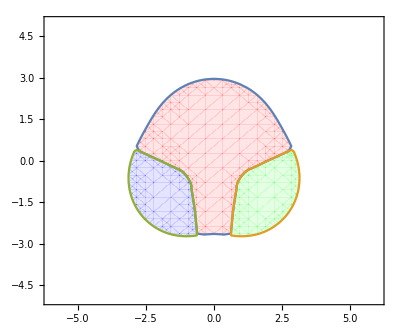

```mathematica
rp=RegionPlot[
{
AssociatedNuclearAttractor[w,ncps,{0.,y,z},BetaSphereRadii->beta0]==1,
AssociatedNuclearAttractor[w,ncps,{0.,y,z},BetaSphereRadii->beta0]==2,
AssociatedNuclearAttractor[w,ncps,{0.,y,z},BetaSphereRadii->beta0]==3
},
{y,bbymin,bbymax},
{z,bbzmin,bbzmax}
,PlotStyle->{
Directive[Red,Opacity[0.10]],
Directive[Green,Opacity[0.10]],
Directive[Blue,Opacity[0.10]]
}
,AspectRatio->Automatic]
```

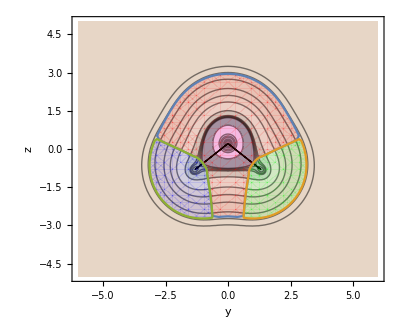

```mathematica
Show[
rhoPlot,
Graphics[bondPathLines],
rp
]
```

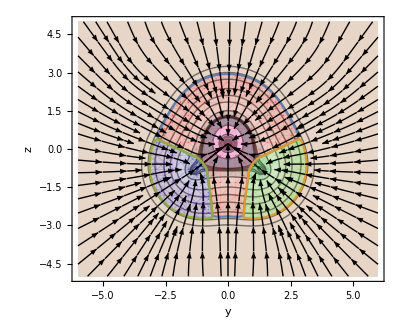

```mathematica
Show[
rhoPlot,
Graphics[bondPathLines],
rp,
streamPlot
]
```

Zoom in on the detail of the one of the bond critical points:

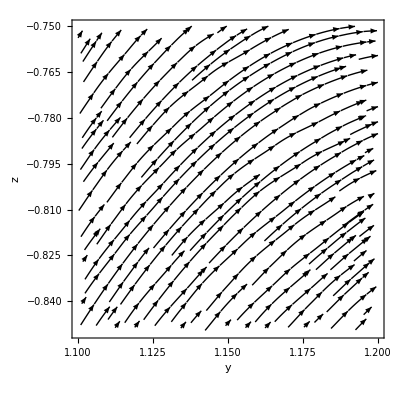

```mathematica
streamPlotZoom=StreamPlot[
gyz[w,{y,z}],
{y,1.10,1.20},
{z,-0.85,-0.75},
FrameLabel->{"y","z"}
,StreamStyle->Black
,StreamColorFunction->None
,AspectRatio->Automatic]
```

Annotate with bond critical point:

```mathematica
Show[
streamPlotZoom,
Graphics[{Red,Disk[bcps[[1,2;;3]],0.0025]}]
]
```

-Graphics-

One of the purposes of this package is to facilitate graphics and plots.  Here, it is shown how to draw individual components so that only the necessary regions are plotted. (Otherwise, graphics get complicated and occluded.)

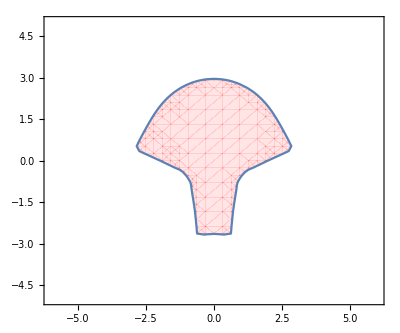

```mathematica
rpO=RegionPlot[
AssociatedNuclearAttractor[w,ncps,{0.,y,z},BetaSphereRadii->beta0]==1,
{y,bbymin,bbymax},
{z,bbzmin,bbzmax}
,PlotStyle->Directive[Red,Opacity[0.10]]
,AspectRatio->Automatic
]
```

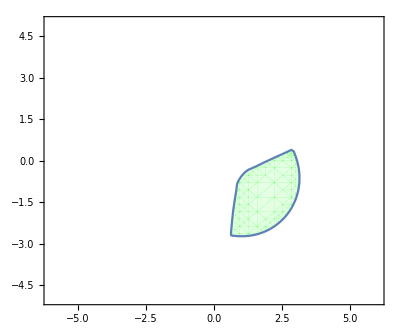

```mathematica
rpH1=RegionPlot[
AssociatedNuclearAttractor[w,ncps,{0.,y,z},BetaSphereRadii->beta0]==2,
{y,bbymin,bbymax},
{z,bbzmin,bbzmax}
,PlotStyle->Directive[Green,Opacity[0.10]]
,AspectRatio->Automatic
]
```

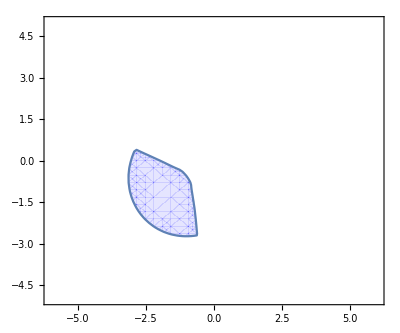

```mathematica
rpH2=RegionPlot[
AssociatedNuclearAttractor[w,ncps,{0.,y,z},BetaSphereRadii->beta0]==3,
{y,bbymin,bbymax},
{z,bbzmin,bbzmax}
,PlotStyle->Directive[Blue,Opacity[0.10]]
,AspectRatio->Automatic
]
```

3D Basin plots can be generated in the same way. Note that increasing PlotPoints makes them smoother, with an increase in computer time.

```mathematica
rp3D=RegionPlot3D[
{
AssociatedNuclearAttractor[w,ncps,{x,y,z},BetaSphereRadii->beta0]==1,
AssociatedNuclearAttractor[w,ncps,{x,y,z},BetaSphereRadii->beta0]==2,
AssociatedNuclearAttractor[w,ncps,{x,y,z},BetaSphereRadii->beta0]==3
},
{x,bbxmin,bbxmax},
{y,bbymin,bbymax},
{z,bbzmin,bbzmax}
,PlotStyle->{
Directive[Red,Opacity[0.10]],
Directive[Green,Opacity[0.10]],
Directive[Blue,Opacity[0.10]]
}
,BoxRatios->Automatic
]
```

-Graphics3D-

```mathematica
rp3DO=RegionPlot3D[
AssociatedNuclearAttractor[w,ncps,{x,y,z},BetaSphereRadii->beta0]==1,
{x,bbxmin,bbxmax},
{y,bbymin,bbymax},
{z,bbzmin,bbzmax}
,PlotStyle->Directive[Red,Opacity[0.10]]
,BoxRatios->Automatic
]
```

-Graphics3D-

```mathematica
rp3DH1=RegionPlot3D[
AssociatedNuclearAttractor[w,ncps,{x,y,z},BetaSphereRadii->beta0]==2,
{x,bbxmin,bbxmax},
{y,bbymin,bbymax},
{z,bbzmin,bbzmax}
,PlotStyle->Directive[Green,Opacity[0.10]]
,BoxRatios->Automatic
]
```

-Graphics3D-

```mathematica
rp3DH2=RegionPlot3D[
AssociatedNuclearAttractor[w,ncps,{x,y,z},BetaSphereRadii->beta0]==3,
{x,bbxmin,bbxmax},
{y,bbymin,bbymax},
{z,bbzmin,bbzmax}
,PlotStyle->Directive[Blue,Opacity[0.10]]
,BoxRatios->Automatic
]
```

-Graphics3D-

```mathematica
rp3DOnomesh=RegionPlot3D[
AssociatedNuclearAttractor[w,ncps,{x,y,z},BetaSphereRadii->beta0]==1,
{x,bbxmin,bbxmax},
{y,bbymin,bbymax},
{z,bbzmin,bbzmax}
,PlotStyle->Directive[Red,Opacity[0.10]]
,Mesh->None
,BoxRatios->Automatic
]
```

-Graphics3D-

```mathematica
rp3DH1nomesh=RegionPlot3D[
AssociatedNuclearAttractor[w,ncps,{x,y,z},BetaSphereRadii->beta0]==2,
{x,bbxmin,bbxmax},
{y,bbymin,bbymax},
{z,bbzmin,bbzmax}
,PlotStyle->Directive[Green,Opacity[0.10]]
,Mesh->None
,BoxRatios->Automatic
]
```

-Graphics3D-

```mathematica
rp3DH2nomesh=RegionPlot3D[
AssociatedNuclearAttractor[w,ncps,{x,y,z},BetaSphereRadii->beta0]==3,
{x,bbxmin,bbxmax},
{y,bbymin,bbymax},
{z,bbzmin,bbzmax}
,PlotStyle->Directive[Blue,Opacity[0.10]]
,Mesh->None
,BoxRatios->Automatic
]
```

-Graphics3D-

## Atomic Properties with Integration over Basins in Cartesian Space

(Note that AccuracyGoals are for demo purposes only.  Some analyses require increased accuracy/precision.)

It turns out beneficial to develop an integration strategy prior to integrating the irregular atomic basins.  Here, we compare what Automatic gives, GlobalAdaptive, vs. LocalAdaptive.  Please note these integrations are in Cartesian space and not in e.g. traditional Spherical Polar coordinates as rays shooting out, starting on a nuclear attractor.  The hope is to use adaptive integration where needed in x,y, and z, and avoid strong orientation effects in spherical polar coordinates. (These pervade many plots in QTAIM.)   There is a different type of mis-specification in Lebedev integration: seldom does one want perfect spherical integration either! Cartesian space representation does not suffer from unreachability problems, such as curved surfaces that rays can not reach, though a steepest ascent path exists. Let’s adapt in Cartesian space if possible, and reserve comparisons for a later date, especially adaptive spherical polar integration.

Long story short: Choose LocalAdaptive.

The whole system:

```mathematica
q=AbsoluteTiming[
NIntegrate[
If[rho[w,{x,y,z}]>Min[$QTAIMContoursPositive],
rho[w,{x,y,z}],
0
], 
{x,bbxmin,bbxmax},
{y,bbymin,bbymax},
{z,bbzmin,bbzmax},
Method->{Automatic, "SymbolicProcessing"->0}
,AccuracyGoal->4,PrecisionGoal->Infinity]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.89648 and 0.00334372 for the integral and error estimates.

{6.68422,9.89648}

```mathematica
q=AbsoluteTiming[
NIntegrate[
If[rho[w,{x,y,z}]>Min[$QTAIMContoursPositive],
rho[w,{x,y,z}],
0
], 
{x,bbxmin,bbxmax},
{y,bbymin,bbymax},
{z,bbzmin,bbzmax},
Method->{"GlobalAdaptive", "SymbolicProcessing"->0}
,AccuracyGoal->4,PrecisionGoal->Infinity]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.89648 and 0.00334372 for the integral and error estimates.

{6.62661,9.89648}

LocalAdaptive is much faster than GlobalAdaptive, Automatic gets it wrong every time. I wonder if this is because it can re-use expensive function evaluations! This is contrary to what I expected, since GlobalAdaptive is usually superior:

```mathematica
q=AbsoluteTiming[
NIntegrate[
If[rho[w,{x,y,z}]>Min[$QTAIMContoursPositive],
rho[w,{x,y,z}],
0
], 
{x,bbxmin,bbxmax},
{y,bbymin,bbymax},
{z,bbzmin,bbzmax},
Method->{"LocalAdaptive", "SymbolicProcessing"->0}
,AccuracyGoal->4,PrecisionGoal->Infinity]
]
```

{2.60652,9.89807}

LocalAdaptive is ten times faster!

Parallel Processing:

```mathematica
xrange=Subdivide[bbxmin,bbxmax,2];
yrange=Subdivide[bbymin,bbymax,2];
zrange=Subdivide[bbzmin,bbzmax,2];

q=AbsoluteTiming[
ParallelSum[
NIntegrate[
rho[w,{x,y,z}],
{x,xrange[[ix]],xrange[[ix+1]]},
{y,xrange[[iy]],xrange[[iy+1]]},
{z,xrange[[iz]],xrange[[iz+1]]},
Method->{"LocalAdaptive", "SymbolicProcessing"->0}
,AccuracyGoal->4,PrecisionGoal->Infinity
]
,{ix,Length[xrange]-1}
,{iy,Length[yrange]-1}
,{iz,Length[zrange]-1}
]
]
```

{0.265053,9.99639}

(Slower, but likely due to overhead for a pretty small molecule subdivided into many pieces. Should also increase accuracy since error is additive over these subdivided regions!)

Let's try a different way, employing two mirror-plane symmetry:

```mathematica
q=AbsoluteTiming[
4*NIntegrate[
If[rho[w,{x,y,z}]>Min[$QTAIMContoursPositive],
rho[w,{x,y,z}],
0
],
{x,0,bbxmax},
{y,0,bbymax},
{z,bbzmin,bbzmax},
Method->{Automatic, "SymbolicProcessing"->0}
,AccuracyGoal->4,PrecisionGoal->Infinity]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.47405 and 0.00128743 for the integral and error estimates.

{4.54053,9.8962}

```mathematica
q=AbsoluteTiming[
4*NIntegrate[
If[rho[w,{x,y,z}]>Min[$QTAIMContoursPositive],
rho[w,{x,y,z}],
0
], 
{x,0,bbxmax},
{y,0,bbymax},
{z,bbzmin,bbzmax},
Method->{"GlobalAdaptive", "SymbolicProcessing"->0}
,AccuracyGoal->4,PrecisionGoal->Infinity]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.47405 and 0.00128743 for the integral and error estimates.

{4.55082,9.8962}

```mathematica
q=AbsoluteTiming[
4*NIntegrate[
If[rho[w,{x,y,z}]>Min[$QTAIMContoursPositive],
rho[w,{x,y,z}],
0
], 
{x,0,bbxmax},
{y,0,bbymax},
{z,bbzmin,bbzmax},
Method->{"LocalAdaptive", "SymbolicProcessing"->0}
,AccuracyGoal->4,PrecisionGoal->Infinity]
]
```

{0.576972,9.89556}

Shocking time difference, same integrated charge.

Alternative definition of the envelope, when Associated Nuclear Attractor is not 0. This is probably more like what an atomic basin integration would be like, at least for exterior atoms--terminating by default at the early condition where if ρ <(x0, y0, z0) < Min[$QTAIMContourPositive] then assigned ncp index 0:

Let’s try with LocalAdaptive (skipping GlobalAdaptive this time) for the whole molecule:

```mathematica
qalt=AbsoluteTiming[
NIntegrate[
If[AssociatedNuclearAttractor[w,ncps,{x,y,z},BetaSphereRadii->beta0]!=0,
rho[w,{x,y,z}],
0
], 
{x,bbxmin,bbxmax},
{y,bbymin,bbymax},
{z,bbzmin,bbzmax},
Method->{"LocalAdaptive", "SymbolicProcessing"->0}
,AccuracyGoal->4,PrecisionGoal->Infinity]
]
```

{537.891,9.78388}

It’s a good thing that we spent some time investigating integration technique before tackling harder problems.

Integrate over individual atomic basins, using LocalAdaptive.  It could mean orders of magnitude time difference for an expensive integration:

(Note we can help the integration to locate regions of non-zero density by placing nuclear critical point coordinates in the integration limits.)

```mathematica
qO=AbsoluteTiming[
With[{ncp=1},
4*NIntegrate[
If[AssociatedNuclearAttractor[w,ncps,{x,y,z},BetaSphereRadii->beta0]==ncp,
rho[w,{x,y,z}],
0], 
{x,0,bbxmax},
{y,0,bbymax},
{z,bbzmin,ncps[[ncp,3]],bbzmax},
Method->{"LocalAdaptive", "SymbolicProcessing"->0}
,AccuracyGoal->4,PrecisionGoal->Infinity]
]
]
```

{214.32,8.83892}

```mathematica
qH1andH2=AbsoluteTiming[
With[{ncp=2},
4*NIntegrate[
If[AssociatedNuclearAttractor[w,ncps,{x,y,z},BetaSphereRadii->beta0]==ncp,
rho[w,{x,y,z}],
0], 
{x,0,bbxmax},
{y,0,ncps[[ncp,2]],bbymax},
{z,bbzmin,ncps[[ncp,3]],bbzmax},
Method->{"LocalAdaptive", "SymbolicProcessing"->0}
,AccuracyGoal->4,PrecisionGoal->Infinity]
]
]
```

{88.194,0.583129}

Total atomic charge as sum of components:

```mathematica
(qO+qH1andH2)
```

{302.514,9.42205}

Difference between whole molecule and fragments:

```mathematica
Last[qalt]-(Last[qO]+Last[qH1andH2])
```

0.361833

Integrate the Laplacian (should be zeros for each integration, by zero-flux condition). We will use the LocalAdaptive strategy, but it is really a different type of integral and we should come back and compare with GlobalAdaptive/Automatic.  It is known that there are problems integrating to values that are nearly 0, and so some warnings may appear.  Traditionally this is used as a check for the quality of the basin delineation, but here all grids are different because all integrands are different and adaptively sampled with regard to basin and integral value!

```mathematica
L=AbsoluteTiming[
NIntegrate[
If[rho[w,{x,y,z}]>Min[$QTAIMContoursPositive],
laprho[w,{x,y,z}],
0
],
{x,bbxmin,bbxmax},
{y,bbymin,bbymax},
{z,bbzmin,bbzmax},
Method->{"LocalAdaptive", "SymbolicProcessing"->0}
,AccuracyGoal->4,PrecisionGoal->Infinity]
]
```

{2906.59,-0.747796}

The integrated Laplacian density should be zero if truly a quantum (sub)system bound by the zero-flux condition:

```mathematica
LO=AbsoluteTiming[
With[{ncp=1},
4*NIntegrate[
If[AssociatedNuclearAttractor[w,ncps,{x,y,z},BetaSphereRadii->beta0]==ncp,
laprho[w,{x,y,z}],
0], 
{x,0,bbxmax},
{y,0,bbymax},
{z,bbzmin,bbzmax},
Method->{"LocalAdaptive", "SymbolicProcessing"->0}
,AccuracyGoal->4,PrecisionGoal->Infinity]
]
]
```

{1773.27,-1.06619}

```mathematica
LH1andH2=AbsoluteTiming[
With[{ncp=2},
4*NIntegrate[
If[AssociatedNuclearAttractor[w,ncps,{x,y,z},BetaSphereRadii->beta0]==ncp,
laprho[w,{x,y,z}],
0], 
{x,0,bbxmax},
{y,0,bbymax},
{z,bbzmin,bbzmax},
Method->{"LocalAdaptive", "SymbolicProcessing"->0}
,AccuracyGoal->4,PrecisionGoal->Infinity]
]
]
```

{737.908,-0.29405}

```mathematica
(LO+LH1andH2)
```

{2511.17,-1.36024}

```mathematica
Last[L]-(Last[LO]+Last[LH1andH2])
```

0.612442

### Volume

```mathematica
v=AbsoluteTiming[
NIntegrate[
If[rho[w,{x,y,z}]>Min[$QTAIMContoursPositive],
1,
0
], 
{x,bbxmin,bbxmax},
{y,bbymin,bbymax},
{z,bbzmin,bbzmax},
Method->{"LocalAdaptive", "SymbolicProcessing"->0}
,AccuracyGoal->4,PrecisionGoal->Infinity]
]
```

{84.1175,136.477}

```mathematica
vO=AbsoluteTiming[
With[{ncp=1},
4*NIntegrate[
If[AssociatedNuclearAttractor[w,ncps,{x,y,z},BetaSphereRadii->beta0]==ncp,
1,
0], 
{x,0,bbxmax},
{y,0,bbymax},
{z,bbzmin,ncps[[ncp,3]],bbzmax},
Method->{"LocalAdaptive", "SymbolicProcessing"->0}
,AccuracyGoal->2,PrecisionGoal->Infinity]
]
]
```

{148.983,75.3168}

```mathematica
vH1andH2=AbsoluteTiming[
With[{ncp=2},
4*NIntegrate[
If[AssociatedNuclearAttractor[w,ncps,{x,y,z},BetaSphereRadii->beta0]==ncp,
1,
0], 
{x,0,bbxmax},
{y,0,ncps[[ncp,2]],bbymax},
{z,bbzmin,ncps[[ncp,3]],bbzmax},
Method->{"LocalAdaptive", "SymbolicProcessing"->0}
,AccuracyGoal->2,PrecisionGoal->Infinity]
]
]
```

{69.9489,17.328}

```mathematica
vO+2*vH1andH2
```

{288.88,109.973}

## Spherical Polar Basin Delineation and Integration

### Interatomic Surface Radius Plot

InteratomicSurface is a function that returns the {position, radius, and associated nuclear critical points} at a parametric ray shooting from a nuclear critical point along θ and ϕ.

```mathematica
(InteratomicSurface[w,ncps,1,{-3π/4,-π/8},BetaSphereRadii->beta0])[[2]]
```

2.84567

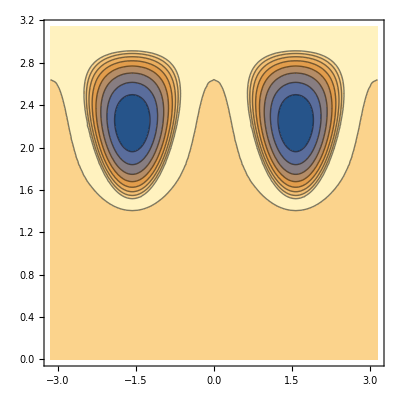

```mathematica
ias1ContourPlot=ContourPlot[
(InteratomicSurface[w,ncps,1,{theta,phi},BetaSphereRadii->beta0])[[2]]
,{phi,-π,π}
,{theta,0,π}
,PlotRange->All]
```

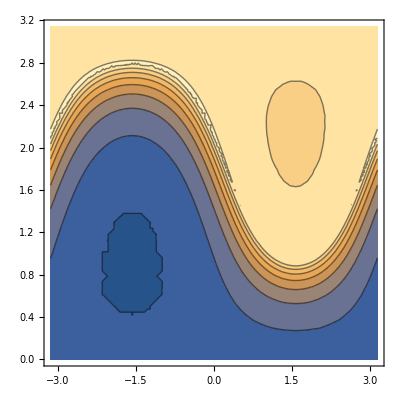

```mathematica
ias2ContourPlot=ContourPlot[
(InteratomicSurface[w,ncps,2,{theta,phi},BetaSphereRadii->beta0])[[2]]
,{phi,-π,π}
,{theta,0,π}
,PlotRange->All]
```

```mathematica
ias3ContourPlot=ContourPlot[
(InteratomicSurface[w,ncps,3,{theta,phi},BetaSphereRadii->beta0])[[2]]
,{phi,-π,π}
,{theta,0,π}
,PlotRange->All]
```

-Graphics-

### Hermite Polynomial Representation of rmax as a function of {θ, ϕ}

```mathematica
Options[FunctionInterpolation]
```

{AccuracyGoal→Automatic,InterpolationOrder→3,InterpolationPoints→11,InterpolationPrecision→Automatic,MaxRecursion→6,PrecisionGoal→Automatic}

```mathematica
iasFunctionInterpolation=ParallelTable[
FunctionInterpolation[
(InteratomicSurface[w,ncps,i,{theta,phi},BetaSphereRadii->beta0])[[2]]
,{theta,N[0],N[π]}
,{phi,N[-π],N[π]}
]
,{i,1,Length[ncps],1}
,Method->"FinestGrained"
];
```

```mathematica
ContourPlot[
(iasFunctionInterpolation[[1]])[theta,phi],
{phi,-π,π},
{theta,0,π}
,PlotRange->All]
```

-Graphics-

```mathematica
ContourPlot[
(iasFunctionInterpolation[[2]])[theta,phi],
{phi,-π,π},
{theta,0,π}
,PlotRange->All]
```

-Graphics-

```mathematica
ContourPlot[
(iasFunctionInterpolation[[3]])[theta,phi],
{phi,-π,π},
{theta,0,π}
,PlotRange->All]
```

-Graphics-

### Partitioning Radial and Angular Components

Split the integration into radial and angular components. Define a function that determines the radial limit and then integrates an arbitrary function f:

```mathematica
Yf[w_,ncps_,ncp_,{theta_?NumericQ,phi_?NumericQ},f_]:=Module[
{rmax},
rmax=(InteratomicSurface[w,ncps,ncp,{theta,phi},BetaSphereRadii->beta0,MaxIterations->10])[[2]];
NIntegrate[
r^2f[w,{r Cos[phi] Sin[theta],r Sin[phi] Sin[theta],r Cos[theta]}+ncps[[ncp]]]
,{r,N[0],N[rmax]}
,Method->{"LocalAdaptive","SymbolicProcessing"->0}
]
];
Yfi[w_,ncps_,ncp_,{theta_?NumericQ,phi_?NumericQ},f_]:=Module[
{rmax},
rmax=(iasFunctionInterpolation[[ncp]])[theta,phi];
NIntegrate[
r^2f[w,{r Cos[phi] Sin[theta],r Sin[phi] Sin[theta],r Cos[theta]}+ncps[[ncp]]]
,{r,N[0],N[rmax]}
,Method->{"LocalAdaptive","SymbolicProcessing"->0}
]
];
```

### Atomic Surface

```mathematica
AbsoluteTiming[
as1=Reap[
With[
{ncp=1},
NIntegrate[
Sin[theta]*
Yf[w,ncps,ncp,{theta,phi},rho]
,{phi,N[-π],N[π]}
,{theta,N[0],N[π]}
,AccuracyGoal->2,PrecisionGoal->Infinity
,Method->{Automatic,"SymbolicProcessing"->0}
,EvaluationMonitor:>Sow[(InteratomicSurface[w,ncps,ncp,{theta,phi},BetaSphereRadii->beta0])[[1]]]
]
]
];
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{720.168,Null}

```mathematica
With[
{ncp=1},
Show[
ListPointPlot3D[as1[[2,1]],ColorFunction->Function[{x,y,z},Black]],
Graphics3D[
Table[
Line[{ncps[[ncp]],as1[[2,1,i]]}]
,{i,1,Length[as1[[2,1]]]}]
,Gray],
graph,
BoxRatios->Automatic
,PlotRange->All]
]
```

-Graphics3D-

### Electron Density

```mathematica
(* Experimental
f[theta_?NumericQ]:=Sin[theta]*NIntegrate[
Yf[w,ncps,1,{theta,phi},rho]
,{phi,N[0],N[π]}
,Method->{"LocalAdaptive","SymbolicProcessing"->0}]
ParallelNInt[f,{N[-π],N[π]},2] *)
```

```mathematica
qO=AbsoluteTiming[
With[{ncp=1},
NIntegrate[
If[AssociatedNuclearAttractor[w,ncps,{x,y,z},BetaSphereRadii->beta0]==ncp,
rho[w,{x,y,z}],
0], 
{x,bbxmin,ncps[[ncp,1]],bbxmax},
{y,bbymin,ncps[[ncp,2]],bbymax},
{z,bbzmin,ncps[[ncp,3]],bbzmax},
Method->{"LocalAdaptive", "SymbolicProcessing"->0}
,AccuracyGoal->2,PrecisionGoal->Infinity]
]
]
```

{42.7339,8.84525}

```mathematica
AbsoluteTiming[
intq1=With[
{ncp=1},
NIntegrate[
Sin[theta]*
Yf[w,ncps,ncp,{theta,phi},rho]
,{phi,N[-π],N[π]}
,{theta,N[0],N[π]}
,AccuracyGoal->2,PrecisionGoal->Infinity
,Method->{"LocalAdaptive","SymbolicProcessing"->0}
]
]
]
```

{78.0846,8.8292}

```mathematica
qO=AbsoluteTiming[
With[{ncp=1},
NIntegrate[
If[AssociatedNuclearAttractor[w,ncps,{x,y,z},BetaSphereRadii->beta0]==ncp,
rho[w,{x,y,z}],
0], 
{x,bbxmin,ncps[[ncp,1]],bbxmax},
{y,bbymin,ncps[[ncp,2]],bbymax},
{z,bbzmin,ncps[[ncp,3]],bbzmax},
Method->{"LocalAdaptive", "SymbolicProcessing"->0}
,AccuracyGoal->3,PrecisionGoal->Infinity]
]
]
```

{115.433,8.83648}

```mathematica
AbsoluteTiming[
intq1=With[
{ncp=1},
NIntegrate[
Sin[theta]*
Yf[w,ncps,ncp,{theta,phi},rho]
,{phi,N[-π],N[π]}
,{theta,N[0],N[π]}
,AccuracyGoal->3,PrecisionGoal->Infinity
,Method->{"LocalAdaptive","SymbolicProcessing"->0}
]
]
]
```

{255.15,8.83347}

```mathematica
qO=AbsoluteTiming[
With[{ncp=1},
NIntegrate[
If[AssociatedNuclearAttractor[w,ncps,{x,y,z},BetaSphereRadii->beta0]==ncp,
rho[w,{x,y,z}],
0], 
{x,bbxmin,ncps[[ncp,1]],bbxmax},
{y,bbymin,ncps[[ncp,2]],bbymax},
{z,bbzmin,ncps[[ncp,3]],bbzmax},
Method->{"LocalAdaptive", "SymbolicProcessing"->0}
,AccuracyGoal->4,PrecisionGoal->Infinity]
]
]
```

{824.813,8.83892}

```mathematica
AbsoluteTiming[
intq1=With[
{ncp=1},
NIntegrate[
Sin[theta]*
Yf[w,ncps,ncp,{theta,phi},rho]
,{phi,N[-π],N[π]}
,{theta,N[0],N[π]}
,AccuracyGoal->4,PrecisionGoal->Infinity
,Method->{"LocalAdaptive","SymbolicProcessing"->0}
]
]
]
```

{1204.57,8.83426}

```mathematica
AbsoluteTiming[
intq2=With[
{ncp=2},
NIntegrate[
Sin[theta]*
Yf[w,ncps,ncp,{theta,phi},rho]
,{phi,N[-π],N[π]}
,{theta,N[0],N[π]}
,AccuracyGoal->4,PrecisionGoal->Infinity
,Method->{"LocalAdaptive","SymbolicProcessing"->0}
]
]
]
```

{647.004,0.464007}

```mathematica
AbsoluteTiming[
intq3=With[
{ncp=3},
NIntegrate[
Sin[theta]*
Yf[w,ncps,ncp,{theta,phi},rho]
,{phi,N[-π],N[π]}
,{theta,N[0],N[π]}
,AccuracyGoal->4,PrecisionGoal->Infinity
,Method->{"LocalAdaptive","SymbolicProcessing"->0}
]
]
]
```

{648.556,0.464007}

```mathematica
intq1+intq2+intq3
```

9.76228

### Laplacian of the Electron Density

```mathematica
AbsoluteTiming[
intl1=With[
{ncp=1},
NIntegrate[
Sin[theta]*
Yf[w,ncps,ncp,{theta,phi},laprho]
,{phi,N[-π],N[π]}
,{theta,N[0],N[π]}
,AccuracyGoal->4,PrecisionGoal->Infinity
,Method->{"LocalAdaptive","SymbolicProcessing"->0}
]
]
]
```

```mathematica
AbsoluteTiming[
intl2=With[
{ncp=2},
NIntegrate[
Sin[theta]*
Yf[w,ncps,ncp,{theta,phi},laprho]
,{phi,N[-π],N[π]}
,{theta,N[0],N[π]}
,AccuracyGoal->4,PrecisionGoal->Infinity
,Method->{"LocalAdaptive","SymbolicProcessing"->0}
]
]
]
```

```mathematica
AbsoluteTiming[
intl3=With[
{ncp=3},
NIntegrate[
Sin[theta]*
Yf[w,ncps,ncp,{theta,phi},laprho]
,{phi,N[-π],N[π]}
,{theta,N[0],N[π]}
,AccuracyGoal->4,PrecisionGoal->Infinity
,Method->{"LocalAdaptive","SymbolicProcessing"->0}
]
]
]
```

```mathematica
intl1+intl2+intl3
```

### Kinetic Energy Density G

```mathematica
AbsoluteTiming[
intg1=With[
{ncp=1},
NIntegrate[
Sin[theta]*
Yf[w,ncps,ncp,{theta,phi},KineticEnergyDensityG]
,{phi,N[-π],N[π]}
,{theta,N[0],N[π]}
,AccuracyGoal->4,PrecisionGoal->Infinity
,Method->{"LocalAdaptive","SymbolicProcessing"->0}
]
]
]
```

```mathematica
AbsoluteTiming[
intg2=With[
{ncp=2},
NIntegrate[
Sin[theta]*
Yf[w,ncps,ncp,{theta,phi},KineticEnergyDensityG]
,{phi,N[-π],N[π]}
,{theta,N[0],N[π]}
,AccuracyGoal->4,PrecisionGoal->Infinity
,Method->{"LocalAdaptive","SymbolicProcessing"->0}
]
]
]
```

```mathematica
AbsoluteTiming[
intg3=With[
{ncp=3},
NIntegrate[
Sin[theta]*
Yf[w,ncps,ncp,{theta,phi},KineticEnergyDensityG]
,{phi,N[-π],N[π]}
,{theta,N[0],N[π]}
,AccuracyGoal->4,PrecisionGoal->Infinity
,Method->{"LocalAdaptive","SymbolicProcessing"->0}
]
]
]
```

```mathematica
intg1+intg2+intg3
```

### Kinetic Energy Density K

```mathematica
AbsoluteTiming[
intk1=With[
{ncp=1},
NIntegrate[
Sin[theta]*
Yf[w,ncps,ncp,{theta,phi},KineticEnergyDensityK]
,{phi,N[-π],N[π]}
,{theta,N[0],N[π]}
,AccuracyGoal->4,PrecisionGoal->Infinity
,Method->{"LocalAdaptive","SymbolicProcessing"->0}
]
]
]
```

```mathematica
AbsoluteTiming[
intk2=With[
{ncp=2},
NIntegrate[
Sin[theta]*
Yf[w,ncps,ncp,{theta,phi},KineticEnergyDensityK]
,{phi,N[-π],N[π]}
,{theta,N[0],N[π]}
,AccuracyGoal->4,PrecisionGoal->Infinity
,Method->{"LocalAdaptive","SymbolicProcessing"->0}
]
]
]
```

```mathematica
AbsoluteTiming[
intk3=With[
{ncp=3},
NIntegrate[
Sin[theta]*
Yf[w,ncps,ncp,{theta,phi},KineticEnergyDensityK]
,{phi,N[-π],N[π]}
,{theta,N[0],N[π]}
,AccuracyGoal->4,PrecisionGoal->Infinity
,Method->{"LocalAdaptive","SymbolicProcessing"->0}
]
]
]
```

```mathematica
intk1+intk2+intk3
```

### Volume

```mathematica
One[x_,y_]:=1;
AbsoluteTiming[
vint1=With[
{ncp=1},
NIntegrate[
Sin[theta]*
Yf[w,ncps,ncp,{theta,phi},One]
,{phi,N[-π],N[π]}
,{theta,N[0],N[π]}
,AccuracyGoal->2,PrecisionGoal->Infinity
,Method->{"LocalAdaptive","SymbolicProcessing"->0}
]
]
]
```

{3919.5,73.6001}

```mathematica
One[x_,y_]:=1;
AbsoluteTiming[
vint2=With[
{ncp=2},
NIntegrate[
Sin[theta]*
Yf[w,ncps,ncp,{theta,phi},One]
,{phi,N[-π],N[π]}
,{theta,N[0],N[π]}
,AccuracyGoal->2,PrecisionGoal->Infinity
,Method->{"LocalAdaptive","SymbolicProcessing"->0}
]
]
]
```

{1604.25,12.1237}

```mathematica
One[x_,y_]:=1;
AbsoluteTiming[
vint3=With[
{ncp=3},
NIntegrate[
Sin[theta]*
Yf[w,ncps,ncp,{theta,phi},One]
,{phi,N[-π],N[π]}
,{theta,N[0],N[π]}
,AccuracyGoal->2,PrecisionGoal->Infinity
,Method->{"LocalAdaptive","SymbolicProcessing"->0}
]
]
]
```

{1586.66,12.1237}

```mathematica
vint1+vint2+vint3
```

97.8475

## Cerjan-Miller-Baker Approach to Locating Critical Points

The CMB method (introduced to QTAIM by Popelier) is amenable to direct location of stationary points of a particular signature in any field so long as we can provide its gradient and Hessian. In QTAIM we need separate routines for each corresponding to nuclear (-3), bond (-1), ring (+1), and cage (+3) critical points.

```mathematica
rhoPlot
```

-Graphics-

```mathematica
CriticalPointGradientMinus3[
{
g[w,{0,0,1}],
H[w,{0,0,1}]
}]
```

{3.23626×10^-19,1.18208×10^-18,-1.81761}

```mathematica
CriticalPointGradientMinus3[
{
g[w,{0,0,-1}],
H[w,{0,0,-1}]
}]
```

{-8.35476×10^-18,-1.36815×10^-17,2.23496}

```mathematica
CriticalPointRank[{x_,y_,z_}]:=Total[Map[If[#==0,0,1]&,Chop[Eigenvalues[H[w,{x,y,z}]]]]];
CriticalPointSignature[{x_,y_,z_}]:=Total[Map[Which[#<0,-1,#==0,0,#>0,1]&,Chop[Eigenvalues[H[w,{x,y,z}]]]]];
```

```mathematica
AbsoluteTiming[
soln=NDSolveValue[
{
X'[s]==CriticalPointGradientMinus3[
{
g[w,X[s]],
H[w,X[s]]
}],
X[0]=={ncps[[1,1]]+0.005,ncps[[1,2]]+0.005,ncps[[1,3]]-0.005}
},
{X[s]},
{s,0,10000}
(*,Method->"BDF"*)
(*,AccuracyGoal->2,PrecisionGoal->Infinity]*)
]
]
```

{25.2718,{InterpolatingFunction[…][s]}}

```mathematica
ParametricPlot3D[
soln[[1]]
,{s,0,soln[[1,0,1,1,2]]},PlotRange->All]
```

-Graphics3D-

```mathematica
soln=NDSolveValue[
{
X'[s]==CriticalPointGradientMinus1[
{
g[w,X[s]],
H[w,X[s]]
}],
X[0]=={bcps[[1,1]]+0.005,bcps[[1,2]]+0.005,bcps[[1,3]]-0.005}
},
{X[s]},
{s,0,10000}
(*,Method->"BDF"
,AccuracyGoal->2,PrecisionGoal->Infinity*)]
```

```mathematica
soln[[1]]
```

InterpolatingFunction[…][s]

```mathematica
ParametricPlot3D[
soln[[1]]
,{s,0,soln[[1,0,1,1,2]]},PlotRange->All]
```

-Graphics3D-

```mathematica
sf=soln[[1,0,1,1,2]]
```

1.47724×10^-7

```mathematica
First[soln/.{s->soln[[1,0,1,1,2]]}]
```

{0.0055319,0.00001919,0.225367}

```mathematica
FindRoot[
CriticalPointGradientMinus1[
{
g[w,{x,y,z}],
H[w,{x,y,z}]
}]
,{x,bcps[[1,1]]+0.005},{y,bcps[[1,2]]+0.005},{z,bcps[[1,3]]-0.005}
,EvaluationMonitor:>Print[{x,y,z}]
]
```

{0.005,-1.14144,-0.682648}

{0.005,-1.14144,-0.682648}

{0.00500001,-1.14144,-0.682648}

{0.005,-1.14144,-0.682648}

{0.005,-1.14144,-0.682648}

{0.00584397,-1.05317,-0.624054}

{0.00584397,-1.05317,-0.624054}

{0.00584398,-1.05317,-0.624054}

{0.00584397,-1.05317,-0.624054}

{0.00584397,-1.05317,-0.624054}

{0.00486289,-0.974382,-0.580907}

{0.00486289,-0.974382,-0.580907}

{0.0048629,-0.974382,-0.580907}

{0.00486289,-0.974382,-0.580907}

{0.00486289,-0.974382,-0.580907}

{0.00219441,-0.901026,-0.559582}

{0.00219441,-0.901026,-0.559582}

{0.00219443,-0.901026,-0.559582}

{0.00219441,-0.901026,-0.559582}

{0.00219441,-0.901026,-0.559582}

{-0.0000391602,-0.82884,-0.572998}

{-0.0000391602,-0.82884,-0.572998}

{-0.0000391453,-0.82884,-0.572998}

{-0.0000391602,-0.82884,-0.572998}

{-0.0000391602,-0.82884,-0.572998}

{0.0000522522,-0.748024,-0.640551}

{-0.0000300189,-0.820759,-0.579754}

{-0.0000300189,-0.820759,-0.579754}

{-0.000030004,-0.820759,-0.579754}

{-0.0000300189,-0.820759,-0.579754}

{-0.0000300189,-0.820759,-0.579754}

{0.0000571668,-0.735833,-0.654928}

{-0.0000213004,-0.812266,-0.587271}

{-0.0000213004,-0.812266,-0.587271}

{-0.0000212855,-0.812266,-0.587271}

{-0.0000213004,-0.812266,-0.587271}

{-0.0000213004,-0.812266,-0.587271}

{0.0000617959,-0.722893,-0.670323}

{-0.0000129907,-0.803329,-0.595576}

{-0.0000129907,-0.803329,-0.595576}

{-0.0000129758,-0.803329,-0.595576}

{-0.0000129907,-0.803329,-0.595576}

{-0.0000129907,-0.803329,-0.595576}

{0.0000657492,-0.709165,-0.686706}

{-5.11674×10^-6,-0.793913,-0.604689}

{-5.11674×10^-6,-0.793913,-0.604689}

{-5.10184×10^-6,-0.793913,-0.604689}

{-5.11674×10^-6,-0.793913,-0.604689}

{-5.11674×10^-6,-0.793913,-0.604689}

{0.0000670345,-0.694611,-0.704031}

{2.09838×10^-6,-0.783982,-0.614623}

{-1.50918×10^-6,-0.788947,-0.609656}

{-1.50918×10^-6,-0.788947,-0.609656}

{-1.49428×10^-6,-0.788947,-0.609656}

{-1.50918×10^-6,-0.788947,-0.609656}

{-1.50918×10^-6,-0.788947,-0.609656}

{0.0000664816,-0.686883,-0.713197}

{5.28989×10^-6,-0.778741,-0.62001}

{1.89036×10^-6,-0.783844,-0.614833}

{1.90587×10^-7,-0.786396,-0.612245}

{-6.59298×10^-7,-0.787672,-0.61095}

{-6.59298×10^-7,-0.787672,-0.61095}

{-6.44396×10^-7,-0.787672,-0.61095}

{-6.59298×10^-7,-0.787672,-0.61095}

{-6.59298×10^-7,-0.787672,-0.61095}

{0.0000667433,-0.68489,-0.715555}

{6.08096×10^-6,-0.777394,-0.621411}

{2.71083×10^-6,-0.782533,-0.616181}

{1.02577×10^-6,-0.785102,-0.613566}

{1.83235×10^-7,-0.786387,-0.612258}

{-2.38031×10^-7,-0.787029,-0.611604}

{-2.38031×10^-7,-0.787029,-0.611604}

{-2.2313×10^-7,-0.787029,-0.611604}

{-2.38031×10^-7,-0.787029,-0.611604}

{-2.38031×10^-7,-0.787029,-0.611604}

{0.000066788,-0.683887,-0.716742}

{6.46457×10^-6,-0.776715,-0.622118}

{3.11327×10^-6,-0.781872,-0.616861}

{1.43762×10^-6,-0.784451,-0.614233}

{5.99794×10^-7,-0.78574,-0.612918}

{1.80881×10^-7,-0.786385,-0.612261}

{-2.85749×10^-8,-0.786707,-0.611933}

{-2.85749×10^-8,-0.786707,-0.611933}

{-1.36737×10^-8,-0.786707,-0.611933}

{-2.85749×10^-8,-0.786707,-0.611933}

{-2.85749×10^-8,-0.786707,-0.611933}

{0.0000663097,-0.683383,-0.717338}

{6.60525×10^-6,-0.776375,-0.622473}

{3.28834×10^-6,-0.781541,-0.617203}

{1.62988×10^-6,-0.784124,-0.614568}

{8.00653×10^-7,-0.785415,-0.61325}

{3.86039×10^-7,-0.786061,-0.612592}

{1.78732×10^-7,-0.786384,-0.612262}

{7.50786×10^-8,-0.786545,-0.612097}

{2.32519×10^-8,-0.786626,-0.612015}

{-2.6615×10^-9,-0.786667,-0.611974}

{-2.6615×10^-9,-0.786667,-0.611974}

{1.22397×10^-8,-0.786667,-0.611974}

{-2.6615×10^-9,-0.786667,-0.611974}

{-2.6615×10^-9,-0.786667,-0.611974}

{0.000066223,-0.68332,-0.717412}

{6.61991×10^-6,-0.776332,-0.622518}

{3.30862×10^-6,-0.781499,-0.617246}

{1.65298×10^-6,-0.784083,-0.61461}

{8.2516×10^-7,-0.785375,-0.613292}

{4.11249×10^-7,-0.786021,-0.612633}

{2.04294×10^-7,-0.786344,-0.612303}

{1.00816×10^-7,-0.786505,-0.612139}

{4.90773×10^-8,-0.786586,-0.612056}

{2.32079×10^-8,-0.786626,-0.612015}

{1.02732×10^-8,-0.786646,-0.611995}

{3.80585×10^-9,-0.786656,-0.611984}

{5.72175×10^-10,-0.786662,-0.611979}

{-1.04466×10^-9,-0.786664,-0.611977}

{-1.04466×10^-9,-0.786664,-0.611977}

{1.38565×10^-8,-0.786664,-0.611977}

{-1.04466×10^-9,-0.786664,-0.611977}

{-1.04466×10^-9,-0.786664,-0.611977}

{0.0000662244,-0.683316,-0.717417}

{6.6215×10^-6,-0.776329,-0.622521}

{3.31023×10^-6,-0.781497,-0.617249}

{1.65459×10^-6,-0.78408,-0.614613}

{8.26773×10^-7,-0.785372,-0.613295}

{4.12864×10^-7,-0.786018,-0.612636}

{2.0591×10^-7,-0.786341,-0.612306}

{1.02433×10^-7,-0.786503,-0.612141}

{5.0694×10^-8,-0.786583,-0.612059}

{2.48246×10^-8,-0.786624,-0.612018}

{1.189×10^-8,-0.786644,-0.611997}

{5.42266×10^-9,-0.786654,-0.611987}

{2.189×10^-9,-0.786659,-0.611982}

{5.72168×10^-10,-0.786662,-0.611979}

{-2.36248×10^-10,-0.786663,-0.611978}

{-2.36248×10^-10,-0.786663,-0.611978}

{1.46649×10^-8,-0.786663,-0.611978}

{-2.36248×10^-10,-0.786663,-0.611978}

{-2.36248×10^-10,-0.786663,-0.611978}

{0.0000662486,-0.683314,-0.71742}

{6.62465×10^-6,-0.776328,-0.622522}

{3.31221×10^-6,-0.781495,-0.61725}

{1.65598×10^-6,-0.784079,-0.614614}

{8.27874×10^-7,-0.785371,-0.613296}

{4.13819×10^-7,-0.786017,-0.612637}

{2.06791×10^-7,-0.78634,-0.612307}

{1.03278×10^-7,-0.786501,-0.612143}

{5.15207×10^-8,-0.786582,-0.61206}

{2.56422×10^-8,-0.786622,-0.612019}

{1.2703×10^-8,-0.786643,-0.611998}

{6.23337×10^-9,-0.786653,-0.611988}

{2.99856×10^-9,-0.786658,-0.611983}

{1.38116×10^-9,-0.78666,-0.61198}

{5.72454×10^-10,-0.786662,-0.611979}

{1.68103×10^-10,-0.786662,-0.611978}

{-3.40723×10^-11,-0.786662,-0.611978}

{-3.40723×10^-11,-0.786662,-0.611978}

{1.48671×10^-8,-0.786662,-0.611978}

{-3.40723×10^-11,-0.786662,-0.611978}

{-3.40723×10^-11,-0.786662,-0.611978}

{0.0000678417,-0.683312,-0.717426}

{6.78414×10^-6,-0.776327,-0.622523}

{3.39205×10^-6,-0.781495,-0.617251}

{1.69601×10^-6,-0.784079,-0.614614}

{8.47988×10^-7,-0.785371,-0.613296}

{4.23977×10^-7,-0.786017,-0.612637}

{2.11971×10^-7,-0.78634,-0.612308}

{1.05969×10^-7,-0.786501,-0.612143}

{5.29673×10^-8,-0.786582,-0.612061}

{2.64666×10^-8,-0.786622,-0.612019}

{1.32163×10^-8,-0.786642,-0.611999}

{6.5911×10^-9,-0.786652,-0.611988}

{3.27851×10^-9,-0.786657,-0.611983}

{1.62222×10^-9,-0.78666,-0.611981}

{7.94074×10^-10,-0.786661,-0.611979}

{3.80001×10^-10,-0.786662,-0.611979}

{1.72964×10^-10,-0.786662,-0.611978}

{6.94461×10^-11,-0.786662,-0.611978}

{1.76869×10^-11,-0.786662,-0.611978}

{-8.19267×10^-12,-0.786662,-0.611978}

{-8.19267×10^-12,-0.786662,-0.611978}

{1.4893×10^-8,-0.786662,-0.611978}

{-8.19267×10^-12,-0.786662,-0.611978}

{-8.19267×10^-12,-0.786662,-0.611978}

{0.000152335,-0.683294,-0.717493}

{0.0000152335,-0.776326,-0.62253}

{7.61673×10^-6,-0.781494,-0.617254}

{3.80836×10^-6,-0.784078,-0.614616}

{1.90418×10^-6,-0.78537,-0.613297}

{9.52085×10^-7,-0.786016,-0.612638}

{4.76038×10^-7,-0.786339,-0.612308}

{2.38015×10^-7,-0.786501,-0.612143}

{1.19003×10^-7,-0.786582,-0.612061}

{5.94976×10^-8,-0.786622,-0.612019}

{2.97447×10^-8,-0.786642,-0.611999}

{1.48683×10^-8,-0.786652,-0.611988}

{7.43003×10^-9,-0.786657,-0.611983}

{3.71092×10^-9,-0.78666,-0.611981}

{1.85136×10^-9,-0.786661,-0.611979}

{9.21586×10^-10,-0.786662,-0.611979}

{4.56696×10^-10,-0.786662,-0.611978}

{2.24252×10^-10,-0.786662,-0.611978}

{1.0803×10^-10,-0.786662,-0.611978}

{4.99185×10^-11,-0.786662,-0.611978}

{2.08629×10^-11,-0.786662,-0.611978}

{6.33511×10^-12,-0.786662,-0.611978}

{-9.28778×10^-13,-0.786662,-0.611978}

{-9.28778×10^-13,-0.786662,-0.611978}

{1.49002×10^-8,-0.786662,-0.611978}

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

FindRoot::nlnum: The function value {ComplexInfinity,ComplexInfinity,ComplexInfinity} is not a list of numbers with dimensions {3} at {x,y,z} = {-9.28778×10^-13,-0.786662,-0.611978}.

{x→-9.28778×10^-13,y→-0.786662,z→-0.611978}

```mathematica
bcps//TableForm
```

0 | -1.14644 | -0.677648 | 3 | -1
0 | 1.14644 | -0.677648 | 3 | -1

```mathematica
(*
FindRoot[
CriticalPointGradientPlus1[
{
g[w,{x,y,z}],
H[w,{x,y,z}]
}]
,{x,rcps[[1,1]]+0.005},{y,rcps[[1,2]]+0.005},{z,rcps[[1,3]]-0.005}
,EvaluationMonitor:>Print[{x,y,z}]
]
*)
```

```mathematica
(*
FindRoot[
CriticalPointGradientPlus3[
{
g[w,{x,y,z}],
H[w,{x,y,z}]
}]
,{x,ccps[[1,1]]+0.005},{y,ccps[[1,2]]+0.005},{z,ccps[[1,3]]-0.005}
,EvaluationMonitor:>Print[{x,y,z}]
]
*)
```

### Parallel Search

A strategy is to make a grid and search for each type of critical point. Let’s start with the integration of the electron density over the system:

```mathematica
q=Reap[
AbsoluteTiming[
NIntegrate[
If[rho[w,{x,y,z}]>Min[$QTAIMContoursPositive],
rho[w,{x,y,z}],
0
], 
{x,bbxmin,bbxmax},
{y,bbymin,bbymax},
{z,bbzmin,bbzmax},
Method->{"LocalAdaptive", "SymbolicProcessing"->0}
,AccuracyGoal->0,PrecisionGoal->Infinity
,EvaluationMonitor:>Sow[{x,y,z}]]
]
];
integrationPoints=q[[2,1]];
```

```mathematica
Show[
ListPointPlot3D[integrationPoints,AspectRatio->Automatic],
graph
,BoxRatios->Automatic
,PlotRange->All
]
```

-Graphics3D-

But this is probably way too many points.  We would reserve this strategy for careful scans of systems of which we knew very little, and are looking for subtle/long-range bond paths, etc.

Example: Offset slightly from the first bond critical point, and then perform CJM gradient ascent to a -1 critical point:

```mathematica
soln=NDSolveValue[
{
X'[s]==CriticalPointGradientMinus1[
{
g[w,X[s]],
H[w,X[s]]
}],
X[0]=={bcps[[1,1]]+0.005,bcps[[1,2]]+0.005,bcps[[1,3]]-0.005}
},
{X[s]},
{s,0,10000}
,Method->"BDF"
,MaxSteps->100
(*,AccuracyGoal->2,PrecisionGoal->Infinity*)]
```

NDSolveValue::mxst: Maximum number of 100 steps reached at the point s == 0.00152688.

{InterpolatingFunction[…][s]}

(The endpoint is buried in the interpolating function object result)

This search starts at each nuclear position and performs a CJM gradient ascent:

```mathematica
AbsoluteTiming[
cpsMinus3=Select[
DeleteDuplicates[
Select[
Select[
ParallelTable[
Quiet[Check[
soln=NDSolveValue[
{
X'[s]==CriticalPointGradientMinus3[
{
g[w,X[s]],
H[w,X[s]]
}],
X[0]==(w["NuclearCartesianCoordinates"])[[i]]
},
{X[s]},
{s,0,10000}
,Method->"BDF"
,MaxSteps->100
(*,AccuracyGoal->4,PrecisionGoal->Infinity*)];
First[soln/.{s->soln[[1,0,1,1,2]]}]
,
{}
]]
,
{i,1,w["NumberOfNuclei"],1}
,Method->"FinestGrained"
]
,Length[#]==3&]
,((bbxmin<=#[[1]]<=bbxmax)&&
(bbymin<=#[[2]]<=bbymax)&&
(bbzmin<=#[[3]]<=bbzmax))&]
,(EuclideanDistance[#1,#2]<1*^-3) &]
,CriticalPointCharacter[#]==3&&CriticalPointSignature[#]==-3&
]
];
```

```mathematica
cpsMinus3//Chop//TableForm
```

{}

A table of starting values in the yz plane:

```mathematica
initialValues=Flatten[
Outer[
List,
{0.},
Subdivide[bbymin,bbymax,10],
Subdivide[bbzmin,bbzmax,10]
]
,2];
```

```mathematica
Show[
ListPointPlot3D[initialValues,AspectRatio->Automatic],
graph
,BoxRatios->Automatic
,PlotRange->All
]
```

-Graphics3D-

```mathematica
AbsoluteTiming[
cpsMinus3=Select[
DeleteDuplicates[
Select[
Select[
ParallelTable[
Quiet[Check[
soln=NDSolveValue[
{
X'[s]==CriticalPointGradientMinus3[
{
g[w,X[s]],
H[w,X[s]]
}],
X[0]==initialValues[[i]]
},
{X[s]},
{s,0,10000}
,Method->"BDF"
,MaxSteps->100
(*,AccuracyGoal->4,PrecisionGoal->Infinity*)];
First[soln/.{s->soln[[1,0,1,1,2]]}]
,
{}
]]
,
{i,1,Length[initialValues],1}
,Method->"FinestGrained"
]
,Length[#]==3&]
,((bbxmin<=#[[1]]<=bbxmax)&&
(bbymin<=#[[2]]<=bbymax)&&
(bbzmin<=#[[3]]<=bbzmax))&]
,(EuclideanDistance[#1,#2]<1*^-3) &]
,CriticalPointCharacter[#]==3&&CriticalPointSignature[#]==-3&
];
]
```

{1.38897,Null}

```mathematica
cpsMinus3//Chop//TableForm
```

{}

Initial values on the same grid, provided they are enclosed by min/max of NCP coordinates (heuristic):

```mathematica
initialValues=Select[
Flatten[
Outer[
List,
{0.},
Subdivide[bbymin,bbymax,10],
Subdivide[bbzmin,bbzmax,10]
]
,2],
(Min[ncps[[All,1]]]<=#[[1]]<=Max[ncps[[All,1]]]&&
Min[ncps[[All,2]]]<=#[[2]]<=Max[ncps[[All,2]]]&&
Min[ncps[[All,3]]]<=#[[3]]<=Max[ncps[[All,3]]])
&];
```

```mathematica
Show[
ListPointPlot3D[initialValues,AspectRatio->Automatic],
graph
,BoxRatios->Automatic
,PlotRange->All
]
```

-Graphics3D-

```mathematica
AbsoluteTiming[
cpsMinus1=Select[
DeleteDuplicates[
Select[
Select[
ParallelTable[
Quiet[Check[
soln=NDSolveValue[
{
X'[s]==CriticalPointGradientMinus1[
{
g[w,X[s]],
H[w,X[s]]
}],
X[0]==initialValues[[i]]
},
{X[s]},
{s,0,10000}
,Method->"BDF"
,MaxSteps->100
(*,AccuracyGoal->4,PrecisionGoal->Infinity*)];
First[soln/.{s->soln[[1,0,1,1,2]]}]
,
{}
]]
,
{i,1,Length[initialValues],1}
,Method->"FinestGrained"
]
,Length[#]==3&]
,((bbxmin<=#[[1]]<=bbxmax)&&
(bbymin<=#[[2]]<=bbymax)&&
(bbzmin<=#[[3]]<=bbzmax))&]
,(EuclideanDistance[#1,#2]<1*^-3) &]
,CriticalPointCharacter[#]==3&&CriticalPointSignature[#]==-1&
];
]
```

{0.071329,Null}

```mathematica
cpsMinus1//Chop//TableForm
```

{}

```mathematica
AbsoluteTiming[
cpsPlus1=Select[
DeleteDuplicates[
Select[
Select[
ParallelTable[
Quiet[Check[
soln=NDSolveValue[
{
X'[s]==CriticalPointGradientPlus1[
{
g[w,X[s]],
H[w,X[s]]
}],
X[0]==initialValues[[i]]
},
{X[s]},
{s,0,10000}
,Method->"BDF"
,MaxSteps->100
(*,AccuracyGoal->4,PrecisionGoal->Infinity*)];
First[soln/.{s->soln[[1,0,1,1,2]]}]
,
{}
]]
,
{i,1,Length[initialValues],1}
,Method->"FinestGrained"
]
,Length[#]==3&]
,((bbxmin<=#[[1]]<=bbxmax)&&
(bbymin<=#[[2]]<=bbymax)&&
(bbzmin<=#[[3]]<=bbzmax))&]
,(EuclideanDistance[#1,#2]<1*^-3) &]
,CriticalPointCharacter[#]==3&&CriticalPointSignature[#]==+1&
];
]
```

{0.15949,Null}

```mathematica
cpsPlus1//Chop//TableForm
```

{}

```mathematica
AbsoluteTiming[
cpsPlus3=Select[
DeleteDuplicates[
Select[
Select[
ParallelTable[
Quiet[Check[
soln=NDSolveValue[
{
X'[s]==CriticalPointGradientPlus3[
{
g[w,X[s]],
H[w,X[s]]
}],
X[0]==initialValues[[i]]
},
{X[s]},
{s,0,10000}
,Method->"BDF"
,MaxSteps->100
(*,AccuracyGoal->4,PrecisionGoal->Infinity*)];
First[soln/.{s->soln[[1,0,1,1,2]]}]
,
{}
]]
,
{i,1,Length[initialValues],1}
,Method->"FinestGrained"
]
,Length[#]==3&]
,((bbxmin<=#[[1]]<=bbxmax)&&
(bbymin<=#[[2]]<=bbymax)&&
(bbzmin<=#[[3]]<=bbzmax))&]
,(EuclideanDistance[#1,#2]<1*^-3) &]
,CriticalPointCharacter[#]==3&&CriticalPointSignature[#]==+3&
];
]
```

{0.155389,Null}

```mathematica
cpsPlus3//Chop//TableForm
```

{}

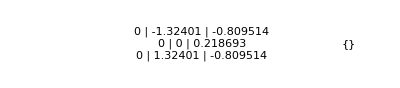

```mathematica
GraphicsRow[
{
ncps//Chop//Sort//TableForm,
cpsMinus3//Chop//Sort//TableForm
}
]
```

```mathematica
GraphicsRow[
{
bcps//Chop//Sort//TableForm,
cpsMinus1//Chop//Sort//TableForm
}
]
```

-Graphics-

```mathematica
GraphicsRow[
{
rcps//Chop//Sort//TableForm,
cpsPlus1//Chop//Sort//TableForm
}
]
```

-Graphics-

```mathematica
GraphicsRow[
{
ccps//Chop//Sort//TableForm,
cpsPlus3//Chop//Sort//TableForm
}
]
```

-Graphics-

## Miscellaneous

Classic examples from traditional QTAIM and Bader’s AIM book.

Enclosing envelope at “0.001 a.u.”

Mesh:

```mathematica
envMesh=ContourPlot3D[
rho[w,{x,y,z}],
{x,bbxmin,bbxmax},
{y,bbymin,bbymax},
{z,bbzmin,bbzmax},
AxesLabel->{"x","y","z"},
Contours->{0.001},
PlotRange->All
,ContourStyle->Opacity[0.25]
,ColorFunctionScaling->True
,BoxRatios->Automatic
]
```

-Graphics3D-

```mathematica
Show[
envMesh,
graph
]
```

-Graphics3D-

Solid:

```mathematica
envRegion=RegionPlot3D[
rho[w,{x,y,z}]>0.001,
{x,bbxmin,bbxmax},
{y,bbymin,bbymax},
{z,bbzmin,bbzmax},
AxesLabel->{"x","y","z"},
PlotRange->All
,PlotStyle->Opacity[0.25]
,ColorFunctionScaling->True
,BoxRatios->Automatic]
```

-Graphics3D-

```mathematica
Show[
envRegion,
graph
]
```

-Graphics3D-

Zero Laplacian Surface:

```mathematica
ContourPlot3D[
-laprho[w,{x,y,z}],
{x,bbxmin,bbxmax},
{y,bbymin,bbymax},
{z,bbzmin,bbzmax},
AxesLabel->{"x","y","z"},
Contours->{0},
PlotRange->All
,ColorFunction->"PearlColors"
,ColorFunctionScaling->True
,BoxRatios->Automatic
]
```

-Graphics3D-

Laplacian in a plane, lone pairs are maxima front/right.

```mathematica
Plot3D[
-laprho[w,{0,y,z}],
{y,bbymin,bbymax},
{z,bbzmin,bbzmax},
AxesLabel->{"x","y","z"}
,PlotPoints->50
,PlotRange->{Full,Full,{-1*^0,1*^0}}
,ColorFunction->"PearlColors"
,ColorFunctionScaling->True
,BoxRatios->Automatic
]
```

-Graphics3D-

## Energy Decomposition over Atomic Basins

```mathematica
w["Energy"]
```

```mathematica
E=Vnn+Vne+Vee+Tn+Te
```

## Tetrahedrane

Showcase tetrahedrane, where all possible critical point types are represented, as a demonstration of fairly comprehensive functionality:

-Graphics3D-

## Epilogue

```mathematica
Uninstall[link]
ParallelEvaluate[Uninstall[link]]
```